```mathematica
(* 
A.Odrzywolek, NSE abundance data, Atomic Data and Nuclear Data Tables 98 (2012) 852-861
*)
```

```mathematica
Date[]
```

{2017,5,11,15,32,17.829633}

```mathematica
$Version
```

11.1.0 for Linux x86 (64-bit) (March 13, 2017)

```mathematica
(* 800 isotopes NSE calculation, MAX 3181 from Wolfram database, 64-bit OS required(!?) for all nuclides *)
```

```mathematica
Directory[]
```

/home/misiek/tmp/libNSE

```mathematica
(* SetDirectory["H://misiek//nse//datasetADNDTfigs/"] *)
```

```mathematica
(* 
SetDirectory["/mnt/E/temp/NSE_pn_table_tmp/"]
*)
```

```mathematica
myPrecision=96
```

96

```mathematica
MinPrecision=Max[50,myPrecision]
```

96

```mathematica
(* range of temperatures [MeV] and densities [kg/m^3] with grid size *)
```

```mathematica
(*T9tbl=Rationalize[{0.1,0.15,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,6.0,7.0,8.0,9.0,10.0},0.001] *)(* T9 from Hix&Thielemann nse.f*)
```

```mathematica
(* kTtoT9=116045/10000 *)
```

```mathematica
(* kTtbl=T9tbl/kTtoT9 *)
```

```mathematica
(* tempMAX=kTtbl[[-1]] *)
```

```mathematica
(* tempMIN=kTtbl[[1]] *)
```

```mathematica
(* Table[kTtbl[[ii]]-kTtbl[[ii-1]]//N,{ii,2,tempNum}]*)
```

```mathematica
tempMAX=1.0 //Rationalize
```

1

```mathematica
tempMIN=0.3 //Rationalize
```

3/10

```mathematica
Δtemp=0.05 //Rationalize
(* NOTE that temperature step must be small enough to provide accurate guess for the next step. Procedure starts with analytical approximation for p, n, He4 mixture for highest temperature, and slowly decrease kT. This procedure fails for kT<0.3 if step is too large.
In fact, it is combination of temperature and density, and for highest densities failure is more likely *)
```

1/20

```mathematica
(* tempNum=Dimensions[T9tbl][[1]]*)
```

```mathematica
(* tempNum=Table[,{temp,tempMIN,tempMAX,Δtemp}] //Dimensions //First*)
```

```mathematica
kTtbl=Table[kT,{kT,tempMIN,tempMAX,Δtemp}] ;
```

```mathematica
tempNum=Dimensions[kTtbl][[1]]
```

15

```mathematica
Export["data/kT.dat",ToString[kTtbl//N]<>"\n\n","Text"]
```

data/kT.dat

```mathematica
lgdensMAX=10
```

10

```mathematica
lgdensMIN=6
```

6

```mathematica
Δlgdens=0.5 //Rationalize
```

1/2

```mathematica
lgdenstbl=Table[lgdens,{lgdens,lgdensMIN, lgdensMAX, Δlgdens}]
```

{6,13/2,7,15/2,8,17/2,9,19/2,10}

```mathematica
lgdensNum=lgdenstbl//Dimensions//First
```

9

```mathematica
Export["data/lg_rho.dat",ToString[lgdenstbl//N]<>"\n\n","Text"]
```

data/lg_rho.dat

```mathematica
(* NOTE: it is better to use rational steps for Ye, because numerical
values might look identical, while they are not, e.g.: 0.35, 0.35000000
In worst case you will get repeated or extremely close entries !
*)
```

```mathematica
YeFINE=Table[Ye,{Ye,0.35,0.55,0.025}]//Rationalize (* more dense tabulation in rapid variation region *)
```

{7/20,3/8,2/5,17/40,9/20,19/40,1/2,21/40,11/20}

```mathematica
Ye1=Table[Ye,{Ye,0.05,0.35,0.05}]//Rationalize (* TODO: Ye very small 0.01, 0.001 etc.*; maybe scalling density from Ye=0.1 ? Results does not seem to change...
*)
```

{1/20,1/10,3/20,1/5,1/4,3/10,7/20}

```mathematica
Ye2=Table[Ye,{Ye,0.55,0.95,0.05}]//Rationalize
```

{11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20}

```mathematica
(* YeMAX = Count[Table[Import["E:/temp/np_800_"<>ToString[NumberForm[N[Ye],{4,4}]]<>".dat"],{Ye,ΔYe,0.5,ΔYe}],$Failed]/1000 *)
```

```mathematica
Yetbl=Union[{0,1/1000,1/100},Ye1, YeFINE,Ye2,{99/100,999/1000,1}]//Sort (* Sort is not required, Union should do this *)
```

{0,1/1000,1/100,1/20,1/10,3/20,1/5,1/4,3/10,7/20,3/8,2/5,17/40,9/20,19/40,1/2,21/40,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,99/100,999/1000,1}

```mathematica
YeNum=Yetbl//Dimensions//First
```

29

```mathematica
ToString[Yetbl//N]
```

{0., 0.001, 0.01, 0.05, 0.1, 0.15, 0.2, 0.25, 0.3, 0.35, 0.375, 0.4, 0.425, 0.45, 0.475, 0.5, 0.525, 0.55, 0.6, 0.65, 0.7, 0.75, 0.8, 0.85, 0.9, 0.95, 0.99, 0.999, 1.}

```mathematica
Export["data/Ye.dat",ToString[Yetbl//N]<>"\n\n","Text"]
```

data/Ye.dat

```mathematica
(* iso800=Take[Delete[IsotopeData[],{{9},{18}}],{1,800}] ; *)
(* 
Mechanical use of large databases requires caution. Deleted positions are Helium2 and Lithium3, included in the databases for historical reasons. Lithium3 drastically changes results for large Ye, because it replaces protons! 

For beginners, I recommend use hand-crafted selections below from well-established published sources 
*)
```

```mathematica
isoP={"Neutron","H1","He4","C12","O16","Ti44","Fe54","Fe56","Ni56","Ni62","Co57"};
(* Minimal astrophysically-motivated selection of nuclides *)
```

```mathematica
iso32={"Neutron","Hydrogen1","He4","C12","O16","Ne20","Mg24","Si28","S32","Ar36","Ca40","Ti44","Ti50","Cr48","Cr54","Cr55","Mn54","Mn55","Mn56","Fe52","Fe54","Fe55","Fe56","Fe57","Fe58","Co55","Co56","Ni56","Ni57","Ni58","Ni60","Zn60"};
(* MPA-Garching HOTB iso32 network *)
```

```mathematica
isoFXT={"Neutron","Hydrogen1","He4","C12","C13","N13","N14","O14","O15","O16","O17","O18","F17","F18","F19","Ne18","Ne19","Ne20","Mg22","Mg24","Al27","Si28","P31","S30","S32","Cl35","Ar36","K39","Ca40","Ti44","Cr48","Cr49","Cr50","Cr51","Cr52","Cr53","Cr54","Fe52","Fe54","Fe55","Fe56","Fe57","Fe58","Co55","Ni56","Ni58"};
(* F.X.Timmes NSE calculations from cococubbed.com *)
```

```mathematica
isoSimplest={"Neutron","Hydrogen1","Helium4"};
(* Simplest possible case. Useful for debugging, analytical estimates, and for high temperatures *)
```

```mathematica
(* NOTE: isotope set must include Neutron and Hydrogen1 *)
```

```mathematica
IsotopeData[Entity["Isotope","Helium4"],"Spin"]
```

0

```mathematica
iso=(IsotopeData[#]&)/@isoP
```

{Entity[Isotope,Neutron],hydrogen,helium-4,carbon-12,oxygen-16,titanium-44,iron-54,iron-56,nickel-56,nickel-62,cobalt-57}

```mathematica
iso[[-1]]//FullForm
```

Entity["Isotope","Cobalt57"]

```mathematica
CommonName@%
```

cobalt-57

```mathematica
CanonicalName@%%
```

Cobalt57

```mathematica
FullForm@%
```

"Cobalt57"

```mathematica
?Entity
```

RowBox[{"Entity", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"type\",\"TI\"]\)\"", ShowStringCharacters->True], ",", StyleBox["name", "TI"]}], "]"}] represents an entity of specified type identified by StyleBox["name", "TI"].

```mathematica
Export["data/isotopes.dat",CanonicalName/@iso]
```

data/isotopes.dat

```mathematica
niso=Dimensions[iso][[1]]
```

11

```mathematica
(* 
BUG?: ponizej potencjalny blad: nie jest oczywiste, ze ostatnie jadro atomowe na liscie ma najwiecej neutronow i protonow! Nalezy przeszukac cala liste 
*)
```

```mathematica
IsotopeData[#,"AtomicNumber"]&/@iso
```

{0,1,2,6,8,22,26,26,28,28,27}

```mathematica
IsotopeData[#,"NeutronNumber"]&/@iso//Max
```

34

```mathematica
(* Zmax=IsotopeData[iso[[-1]],"AtomicNumber"] +3 Max. atomic number *)
(* Nmax=IsotopeData[iso[[-1]],"NeutronNumber"] +2 Max. neutron number *)
```

```mathematica
Zmax=(IsotopeData[#,"AtomicNumber"]&/@iso//Max )(* Max. atomic number *)
Nmax=(IsotopeData[#,"NeutronNumber"]&/@iso//Max)(* Max. neutron number *)
```

28

34

```mathematica
nseH="#define kT_MIN_nse "<>ToString[tempMIN //N] <>"\n"<>
"#define kT_MAX_nse "<>ToString[tempMAX //N] <>"\n"<>
"#define N_kT_nse " <> ToString[tempNum]<>"\n"<>
"#define lg_rho_MIN_nse "<>ToString[lgdensMIN //N] <>"\n"<>
"#define lg_rho_MAX_nse "<>ToString[lgdensMAX //N] <>"\n"<>
"#define N_lg_rho_nse " <> ToString[lgdensNum]<>"\n" <>
"#define N_Ye_nse "<>ToString[YeNum] <>"\n"<>
"#define niso "<>ToString[niso]<>"\n"<>
"#define Z_max_nse "<>ToString[Zmax+1]<>"\n"<>
"#define N_max_nse "<>ToString[Nmax+1]<>"\n";
```

```mathematica
Export["data/nse_tbl.h",nseH,"Text"]
```

data/nse_tbl.h

```mathematica
(* NOTE: It is assumed below that nuclei list is sorted! Last in the list is used to determine max. Z and A *)
```

```mathematica
nuclideTBL=Table[If[Position[iso,IsotopeData[{ii,ii+jj},"StandardName"]]=={},-1,Position[iso,IsotopeData[{ii,ii+jj},"StandardName"]][[1,1]]-1],{ii,1,Zmax},{jj,1,Nmax}];
```

```mathematica
Prepend[Table[-1,{ii,1,Nmax-1}],0] ;
```

```mathematica
Prepend[nuclideTBL,%] ;
```

```mathematica
Transpose[%];
```

```mathematica
Table[If[ii==1,1,-1],{ii,0,Zmax}];
```

```mathematica
Prepend[%%,%];
```

```mathematica
nuclideTBLfinal=Transpose[%];
```

```mathematica
magick={{2,1},{9,8},{17,16},{21,20},{29,28},{51,50},{Nmax+1,Nmax}};
```

```mathematica
MatrixPlot[nuclideTBLfinal, DataReversed->{True,False},Mesh->True, FrameTicks->{ magick,magick,None ,None },ColorRules->{-1->White,_->Black},FrameLabel->{"Z","N"}]
```

-Graphics-

```mathematica
Export["data/Nuclide_chart.pdf",%]
```

data/Nuclide_chart.pdf

```mathematica
Dimensions[nuclideTBLfinal]
```

{29,35}

```mathematica
Export["data/N_Z_tbl.dat",ToString[nuclideTBLfinal]<>"\n","Text"]
```

data/N_Z_tbl.dat

```mathematica
id=Table[{QuantityMagnitude[IsotopeData[iso[[ii]],"BindingEnergy"],"MeV"],IsotopeData[iso[[ii]],"Symbol"],IsotopeData[iso⟦ii⟧,"AtomicNumber"],IsotopeData[iso[[ii]],"NeutronNumber"],IsotopeData[iso[[ii]],"MassNumber"],IsotopeData[iso[[ii]],"Spin"],ii},{ii,1,niso,1}]
```

{{0.,^1n,0,1,1,1/2,1},{0.,^1H,1,0,1,1/2,2},{7.073915,^4He,2,2,4,0,3},{7.680144,^12C,6,6,12,0,4},{7.976206,^16O,8,8,16,0,5},{8.533518,^44Ti,22,22,44,0,6},{8.736344,^54Fe,26,28,54,0,7},{8.790323,^56Fe,26,30,56,0,8},{8.642709,^56Ni,28,28,56,0,9},{8.794549,^62Ni,28,34,62,0,10},{8.741858,^57Co,27,30,57,7/2,11}}

```mathematica
tbl=SetPrecision[id /._Missing->0,myPrecision]//Rationalize;
```

```mathematica
(* SetPrecision[id,100] ;*)
```

```mathematica
X=Table[,{i,1,niso}];
```

```mathematica
(* Temperature dependend partition function *)
```

```mathematica
iso[[-1]]
```

cobalt-57

```mathematica
iso⟦-1⟧
```

cobalt-57

```mathematica
QuantityMagnitude[IsotopeData[iso[[-1]],"ExcitedStateEnergies"],"MeV"]
```

{1.224,1.37766,1.50483,1.69,1.75761,1.8974,1.9195,2.13,2.1331,2.311,2.479,2.486,2.514,2.524,2.56,2.611,2.615,2.723,2.731,2.744,2.80429,2.879,2.981,2.9821,3.1082,3.121,3.165,3.1774,3.184,3.246,3.263,3.272,3.3,3.34,3.357,3.37,3.394,3.43,3.461,3.469,3.522,3.54,3.554,3.622,3.67,3.672,3.681,3.701,3.72,3.72,3.73,3.762,3.77,3.834,3.85,3.854,3.901,3.909,3.918,3.92,3.97,3.991,4.,4.036,4.037,4.046,4.058,4.06,4.111,4.187,4.195,4.217,4.238,4.251,4.272,4.284,4.297,4.308,4.32,4.33,4.357,4.377,4.391,4.399,4.416,4.438,4.448,4.45,4.466,4.475,4.497,4.511,4.52,4.53,4.55,4.576,4.586,4.597,4.608,4.62,4.645,4.659,4.675,4.7,4.72,4.753,4.762,4.772,4.78,4.793,4.801,4.815,4.845,4.853,4.872,4.881,4.911,4.922,4.934,4.948,4.96,4.971,4.98,5.06,5.1,5.14,5.16,5.17,5.22,5.22,5.3,5.38,5.43,5.435,5.46,5.52,5.56,5.572,5.64,5.65,5.707,5.72,5.74,5.757,5.8,5.846,5.88,5.919,5.99,6.01,6.09,6.15,6.18,6.23,6.27,6.31,6.34,6.39,6.4,6.442,6.49,6.5,6.519,6.54,6.59,6.67,6.74,6.77,6.82,6.859,6.9,6.977,7.02,7.07,7.12,7.16,7.19,7.23,7.25,7.27,7.27,7.29,7.3,7.32,7.37,7.4,7.41,7.42,7.42,7.48,7.512,7.528,7.6,7.62,7.64,7.65,7.66,7.71,7.782,7.81,7.84,7.98,7.993,8.06,8.087,8.41,8.633,8.874,9.28,9.318,9.6,9.68,9.69,9.74,9.76,10.077,10.294,11.07,11.292}

```mathematica
FullForm[%[[1]]]
```

1.224

```mathematica
e=Table[SetPrecision[QuantityMagnitude[IsotopeData[iso[[ii]],"ExcitedStateEnergies"],"MeV"],myPrecision] ,{ii,1,niso}]
```

{{},{},{20.2099999999999999999804843608952609201878658495843410491943359375,21.00999999999999999999132638262011596452794037759304046630859375,21.8399999999999999999761475522053189024518360383808612823486328125,23.3299999999999999999848211695852029379238956607878208160400390625,23.639999999999999999986989573930173946791910566389560699462890625,24.25,25.27999999999999999997397914786034789358382113277912139892578125,25.9499999999999999999891579782751449556599254719913005828857421875,27.4200000000000000000151788304147970620761043392121791839599609375,28.3100000000000000000021684043449710088680149056017398834228515625,28.370000000000000000004336808689942017736029811203479766845703125,28.389999999999999999986989573930173946791910566389560699462890625,28.639999999999999999986989573930173946791910566389560699462890625,28.6700000000000000000151788304147970620761043392121791839599609375,29.889999999999999999986989573930173946791910566389560699462890625},{4.43891000000000000001200428645375950509333051741123199462890625,7.6541999999999999999898518676655356784976902417838573455810546875,9.641000000000000000007806255641895631924853660166263580322265625,10.3000000000000000000108420217248550443400745280086994171142578125,10.84400000000000000000520417042793042128323577344417572021484375,11.1600000000000000000238524477946810975481639616191387176513671875,11.827999999999999999997397914786034789358382113277912139892578125,12.7099999999999999999804843608952609201878658495843410491943359375,13.3520000000000000000091072982488782372456626035273075103759765625,14.082999999999999999993061106096092771622352302074432373046875,15.110000000000000000013010426069826053208089433610439300537109375,15.4399999999999999999978315956550289911319850943982601165771484375,16.1058000000000000000014745149545802860302501358091831207275390625,16.5699999999999999999934947869650869733959552831947803497314453125,17.2300000000000000000173472347597680709441192448139190673828125,17.75999999999999999999132638262011596452794037759304046630859375,18.1600000000000000000238524477946810975481639616191387176513671875,18.350000000000000000021684043449710088680149056017398834228515625,18.350000000000000000021684043449710088680149056017398834228515625,18.600000000000000000021684043449710088680149056017398834228515625,18.7099999999999999999804843608952609201878658495843410491943359375,18.8000000000000000000108420217248550443400745280086994171142578125,19.1999999999999999999891579782751449556599254719913005828857421875,19.399999999999999999978315956550289911319850943982601165771484375,19.5500000000000000000108420217248550443400745280086994171142578125,19.6899999999999999999978315956550289911319850943982601165771484375,20.,20.2699999999999999999826527652402319290558807551860809326171875,20.5,20.620000000000000000004336808689942017736029811203479766845703125,20.9800000000000000000173472347597680709441192448139190673828125,21.600000000000000000021684043449710088680149056017398834228515625,22.,22.399999999999999999978315956550289911319850943982601165771484375,22.649999999999999999978315956550289911319850943982601165771484375,23.0400000000000000000195156391047390798121341504156589508056640625,23.5199999999999999999826527652402319290558807551860809326171875,23.9200000000000000000151788304147970620761043392121791839599609375,24.4300000000000000000065052130349130266040447168052196502685546875,24.9200000000000000000151788304147970620761043392121791839599609375,25.3000000000000000000108420217248550443400745280086994171142578125,25.399999999999999999978315956550289911319850943982601165771484375,25.9499999999999999999891579782751449556599254719913005828857421875,26.8000000000000000000108420217248550443400745280086994171142578125,27.,27.59500000000000000002602085213965210641617886722087860107421875,27.899999999999999999978315956550289911319850943982601165771484375,28.1999999999999999999891579782751449556599254719913005828857421875,28.8299999999999999999848211695852029379238956607878208160400390625,29.399999999999999999978315956550289911319850943982601165771484375,29.629999999999999999995663191310057982263970188796520233154296875,30.2900000000000000000195156391047390798121341504156589508056640625,31.1600000000000000000238524477946810975481639616191387176513671875,32.2900000000000000000195156391047390798121341504156589508056640625,33.47000000000000000002602085213965210641617886722087860107421875},{6.049400000000000000009194034422677077600383199751377105712890625,6.1298899999999999999781945259069715348232421092689037322998046875,6.9170999999999999999981785403502243525508674792945384979248046875,7.116849999999999999982132348197438886927557177841663360595703125,8.871900000000000000000520417042793042128323577344417572021484375,9.5849999999999999999804843608952609201878658495843410491943359375,9.84450000000000000001561251128379126384970732033252716064453125,10.3559999999999999999839538078472145343766896985471248626708984375,10.9570000000000000000264545330086463081897818483412265777587890625,11.0799999999999999999848211695852029379238956607878208160400390625,11.0966999999999999999855150589755936607616604305803775787353515625,11.25999999999999999999132638262011596452794037759304046630859375,11.5199999999999999999826527652402319290558807551860809326171875,11.600000000000000000021684043449710088680149056017398834228515625,12.0489999999999999999900253400131333592071314342319965362548828125,12.4399999999999999999978315956550289911319850943982601165771484375,12.52999999999999999997397914786034789358382113277912139892578125,12.795999999999999999981785403502243525508674792945384979248046875,12.9685999999999999999860354760183867028899840079247951507568359375,13.0199999999999999999826527652402319290558807551860809326171875,13.0899999999999999999761475522053189024518360383808612823486328125,13.128999999999999999974846509598336297131027095019817352294921875,13.2590000000000000000247198095326695010953699238598346710205078125,13.6639999999999999999986989573930173946791910566389560699462890625,13.868999999999999999983520126978220332603086717426776885986328125,13.9800000000000000000173472347597680709441192448139190673828125,14.03200000000000000001561251128379126384970732033252716064453125,14.100000000000000000021684043449710088680149056017398834228515625,14.30199999999999999999826527652402319290558807551860809326171875,14.3990000000000000000117093834628434478872804902493953704833984375,14.620000000000000000004336808689942017736029811203479766845703125,14.6600000000000000000238524477946810975481639616191387176513671875,14.8153000000000000000257606436182555853520170785486698150634765625,14.92599999999999999997744859481230150777264498174190521240234375,15.0970000000000000000134441069388202549816924147307872772216796875,15.1960000000000000000143114686768086585288983769714832305908203125,15.25999999999999999999132638262011596452794037759304046630859375,15.4079999999999999999822190843712377272822777740657329559326171875,15.7850000000000000000238524477946810975481639616191387176513671875,15.827999999999999999997397914786034789358382113277912139892578125,16.1999999999999999999891579782751449556599254719913005828857421875,16.20900000000000000001387778780781445675529539585113525390625,16.274999999999999999978315956550289911319850943982601165771484375,16.3520000000000000000091072982488782372456626035273075103759765625,16.4423000000000000000131838984174237339175306260585784912109375,16.816999999999999999985254850454197139697498641908168792724609375,16.84400000000000000000520417042793042128323577344417572021484375,16.9300000000000000000065052130349130266040447168052196502685546875,17.0899999999999999999761475522053189024518360383808612823486328125,17.128999999999999999974846509598336297131027095019817352294921875,17.139999999999999999986989573930173946791910566389560699462890625,17.19699999999999999998091804176425512196146883070468902587890625,17.28200000000000000001561251128379126384970732033252716064453125,17.50999999999999999999132638262011596452794037759304046630859375,17.5550000000000000000065052130349130266040447168052196502685546875,17.608999999999999999992193744358104368075146339833736419677734375,17.72000000000000000002602085213965210641617886722087860107421875,17.774999999999999999978315956550289911319850943982601165771484375,17.7840000000000000000030357660829594124152208678424358367919921875,17.8769999999999999999874232547991681485655135475099086761474609375,18.016000000000000000007806255641895631924853660166263580322265625,18.0290000000000000000073725747729014301512506790459156036376953125,18.089000000000000000009540979117872439019265584647655487060546875,18.201999999999999999976581233074313104225439019501209259033203125,18.2900000000000000000195156391047390798121341504156589508056640625,18.4040000000000000000073725747729014301512506790459156036376953125,18.4300000000000000000065052130349130266040447168052196502685546875,18.483999999999999999992193744358104368075146339833736419677734375,18.600000000000000000021684043449710088680149056017398834228515625,18.600000000000000000021684043449710088680149056017398834228515625,18.639999999999999999986989573930173946791910566389560699462890625,18.7729999999999999999908927017511217627543373964726924896240234375,18.7850000000000000000238524477946810975481639616191387176513671875,18.7900000000000000000195156391047390798121341504156589508056640625,18.9770000000000000000091072982488782372456626035273075103759765625,19.001000000000000000020816681711721685132943093776702880859375,19.0799999999999999999848211695852029379238956607878208160400390625,19.2060000000000000000056378512969246230568387545645236968994140625,19.2530000000000000000082399365108898336984566412866115570068359375,19.2569999999999999999830864461092261308294837363064289093017578125,19.319000000000000000026888213877640509963384829461574554443359375,19.375,19.47000000000000000002602085213965210641617886722087860107421875,19.5389999999999999999986989573930173946791910566389560699462890625,19.753999999999999999974846509598336297131027095019817352294921875,19.808000000000000000014745149545802860302501358091831207275390625,19.8949999999999999999826527652402319290558807551860809326171875,20.0550000000000000000065052130349130266040447168052196502685546875,20.412000000000000000011275702593849246113677509129047393798828125,20.50999999999999999999132638262011596452794037759304046630859375,20.54099999999999999998612221219218554324470460414886474609375,20.5600000000000000000021684043449710088680149056017398834228515625,20.61500000000000000000867361737988403547205962240695953369140625,20.8000000000000000000108420217248550443400745280086994171142578125,20.8570000000000000000047704895589362195096327923238277435302734375,20.9449999999999999999934947869650869733959552831947803497314453125,21.0500000000000000000108420217248550443400745280086994171142578125,21.05199999999999999999826527652402319290558807551860809326171875,21.1750000000000000000108420217248550443400745280086994171142578125,21.5,21.6230000000000000000125767452008318514344864524900913238525390625,21.6479999999999999999908927017511217627543373964726924896240234375,21.775999999999999999999132638262011596452794037759304046630859375,22.0400000000000000000195156391047390798121341504156589508056640625,22.149999999999999999978315956550289911319850943982601165771484375,22.350000000000000000021684043449710088680149056017398834228515625,22.5,22.649999999999999999978315956550289911319850943982601165771484375,22.7209999999999999999926274252270985698487493209540843963623046875,22.889999999999999999986989573930173946791910566389560699462890625,23.,23.100000000000000000021684043449710088680149056017398834228515625,23.235000000000000000013010426069826053208089433610439300537109375,23.50999999999999999999132638262011596452794037759304046630859375,23.878999999999999999974846509598336297131027095019817352294921875,24.0699999999999999999934947869650869733959552831947803497314453125,24.360000000000000000013010426069826053208089433610439300537109375,24.5220000000000000000242861286636752993217669427394866943359375,24.75999999999999999999132638262011596452794037759304046630859375,25.120000000000000000004336808689942017736029811203479766845703125,25.5,25.600000000000000000021684043449710088680149056017398834228515625,26.,26.3630000000000000000212503625807158869065460748970508575439453125,27.350000000000000000021684043449710088680149056017398834228515625,27.5,28.1999999999999999999891579782751449556599254719913005828857421875,28.600000000000000000021684043449710088680149056017398834228515625,29.,29.8000000000000000000108420217248550443400745280086994171142578125,31.8000000000000000000108420217248550443400745280086994171142578125,34.,35.},{1.083050000000000000015785983631388944559148512780666351318359375,1.904299999999999999981091514111852802670910023152828216552734375,2.45429000000000000001991462550421374544384889304637908935546875,2.5310199999999999999930437588613330035514081828296184539794921875,2.8866000000000000000137910516340156164005747996270656585693359375,3.175799999999999999994969301919667259426205419003963470458984375,3.36399999999999999998785693566816235033911652863025665283203125,3.415299999999999999993234578443690452331793494522571563720703125,3.645800000000000000020990154059319365842384286224842071533203125,3.7559000000000000000252402265754625432236935012042522430419921875,3.94269999999999999997814248420269223061040975153446197509765625,3.9800000000000000000173472347597680709441192448139190673828125,4.0153099999999999999869375322258946425790782086551189422607421875,4.0612000000000000000054643789493269423473975621163845062255859375,4.1156000000000000000103216046820620022117509506642818450927734375,4.2270000000000000000091072982488782372456626035273075103759765625,4.4999000000000000000087603535536828758267802186310291290283203125,4.6050000000000000000173472347597680709441192448139190673828125,4.792199999999999999989418186796541476724087260663509368896484375,4.8031000000000000000103216046820620022117509506642818450927734375,4.8399999999999999999761475522053189024518360383808612823486328125,5.0550000000000000000065052130349130266040447168052196502685546875,5.152399999999999999984907905759001778278616257011890411376953125,5.2099999999999999999804843608952609201878658495843410491943359375,5.3050000000000000000065052130349130266040447168052196502685546875,5.420999999999999999981785403502243525508674792945384979248046875,5.6701999999999999999976581233074313104225439019501209259033203125,6.02999999999999999997397914786034789358382113277912139892578125,6.22000000000000000002602085213965210641617886722087860107421875,6.5085000000000000000143114686768086585288983769714832305908203125,6.5724000000000000000000867361737988403547205962240695953369140625,6.60640000000000000000312250225675825276994146406650543212890625,6.8050000000000000000065052130349130266040447168052196502685546875,6.848840000000000000014883927423881004870054312050342559814453125,6.923899999999999999998785693566816235033911652863025665283203125,6.95900000000000000001387778780781445675529539585113525390625,7.2159999999999999999969642339170405875847791321575641632080078125,7.3399999999999999999761475522053189024518360383808612823486328125,7.4084999999999999999926274252270985698487493209540843963623046875,7.5600000000000000000021684043449710088680149056017398834228515625,7.6340000000000000000247198095326695010953699238598346710205078125,7.6700000000000000000151788304147970620761043392121791839599609375,7.6710999999999999999730250499485606496818945743143558502197265625,8.0398999999999999999740658840341467339385417290031909942626953125,8.0400000000000000000195156391047390798121341504156589508056640625,8.066999999999999999985254850454197139697498641908168792724609375,8.1700000000000000000151788304147970620761043392121791839599609375,8.1800000000000000000065052130349130266040447168052196502685546875,8.318000000000000000006071532165918824830441735684871673583984375,8.38499999999999999999132638262011596452794037759304046630859375,8.41599999999999999998612221219218554324470460414886474609375,8.44900000000000000002255140518769849222735501825809478759765625,8.51100000000000000001214306433183764966088347136974334716796875,8.5340000000000000000030357660829594124152208678424358367919921875,8.5649999999999999999978315956550289911319850943982601165771484375,8.6269999999999999999874232547991681485655135475099086761474609375,8.6390000000000000000203830008427274833593401126563549041748046875,8.756000000000000000016479873021779667396913282573223114013671875,8.8615999999999999999812649864594504833803512156009674072265625,8.94699999999999999998091804176425512196146883070468902587890625,8.954000000000000000018214596497756474491325207054615020751953125,8.9599999999999999999804843608952609201878658495843410491943359375,8.9870000000000000000004336808689942017736029811203479766845703125,8.9919999999999999999960968721790521840375731699168682098388671875,9.07300000000000000000173472347597680709441192448139190673828125,9.100000000000000000021684043449710088680149056017398834228515625,9.120000000000000000004336808689942017736029811203479766845703125,9.139999999999999999986989573930173946791910566389560699462890625,9.1800000000000000000065052130349130266040447168052196502685546875,9.2149999999999999999761475522053189024518360383808612823486328125,9.2270000000000000000091072982488782372456626035273075103759765625,9.23899999999999999998785693566816235033911652863025665283203125,9.27999999999999999997397914786034789358382113277912139892578125,9.298000000000000000023418766925686895774560980498790740966796875,9.337999999999999999988724297406150753886322490870952606201171875,9.3609999999999999999796169991572725166406598873436450958251953125,9.3879999999999999999995663191310057982263970188796520233154296875,9.42699999999999999999826527652402319290558807551860809326171875,9.4779999999999999999757138713363247006782330572605133056640625,9.5,9.542000000000000000006938893903907228377647697925567626953125,9.589000000000000000009540979117872439019265584647655487060546875,9.6319999999999999999830864461092261308294837363064289093017578125,9.6679999999999999999735454669913536918102181516587734222412109375,9.69800000000000000000173472347597680709441192448139190673828125,9.712999999999999999988724297406150753886322490870952606201171875,9.7228999999999999999888110335799495942410430870950222015380859375,9.7370000000000000000004336808689942017736029811203479766845703125,9.8730000000000000000125767452008318514344864524900913238525390625,9.8949999999999999999826527652402319290558807551860809326171875,9.9079999999999999999822190843712377272822777740657329559326171875,10.0140000000000000000203830008427274833593401126563549041748046875,10.045999999999999999981785403502243525508674792945384979248046875,10.128999999999999999974846509598336297131027095019817352294921875,10.16599999999999999998612221219218554324470460414886474609375,10.20900000000000000001387778780781445675529539585113525390625,10.2580000000000000000039031278209478159624268300831317901611328125,10.27999999999999999997397914786034789358382113277912139892578125,10.30300000000000000001908195823574487803853116929531097412109375,10.326999999999999999976581233074313104225439019501209259033203125,10.38600000000000000001214306433183764966088347136974334716796875,10.4599999999999999999804843608952609201878658495843410491943359375,10.46369999999999999998161193115464584479923360049724578857421875,10.5199999999999999999826527652402319290558807551860809326171875,10.5899999999999999999761475522053189024518360383808612823486328125,10.860000000000000000013010426069826053208089433610439300537109375,11.08590000000000000001006139616066548114758916199207305908203125,11.54669999999999999997467303725073861642158590257167816162109375,12.1999999999999999999891579782751449556599254719913005828857421875,13.,13.3695999999999999999851681142803982993427780456840991973876953125,14.100000000000000000021684043449710088680149056017398834228515625,14.5500000000000000000108420217248550443400745280086994171142578125,15.4499999999999999999891579782751449556599254719913005828857421875,15.9499999999999999999891579782751449556599254719913005828857421875},{1.408189999999999999992679466931377874061581678688526153564453125,2.5381000000000000000233320307518880554198403842747211456298828125,2.561299999999999999996704025395644066520617343485355377197265625,2.949200000000000000005030698080332740573794580996036529541015625,2.95900000000000000001387778780781445675529539585113525390625,3.16599999999999999998612221219218554324470460414886474609375,3.2947999999999999999784894288978875920292921364307403564453125,3.3447999999999999999893314506227426363693666644394397735595703125,3.4374000000000000000087603535536828758267802186310291290283203125,3.7938000000000000000118828558104411285967216826975345611572265625,3.833199999999999999975540398988727019968791864812374114990234375,3.8409999999999999999969642339170405875847791321575641632080078125,4.0309000000000000000035561831257524545435444451868534088134765625,4.0477999999999999999867293654087774257277487777173519134521484375,4.0716000000000000000159594559789866252685897052288055419921875,4.0996999999999999999937549954864834944601170718669891357421875,4.1033999999999999999948825657458684190714848227798938751220703125,4.2678000000000000000127502175484295321439276449382305145263671875,4.290800000000000000003642919299551294898265041410923004150390625,4.578500000000000000007806255641895631924853660166263580322265625,4.655300000000000000001908195823574487803853116929531097412109375,4.6960000000000000000143114686768086585288983769714832305908203125,4.700099999999999999980397624721462079833145253360271453857421875,4.7819000000000000000243728648374741396764875389635562896728515625,4.948699999999999999994622357224471898007323034107685089111328125,5.0447999999999999999784894288978875920292921364307403564453125,5.0799999999999999999848211695852029379238956607878208160400390625,5.1449999999999999999826527652402319290558807551860809326171875,5.2330000000000000000255871712706579046425758861005306243896484375,5.2480000000000000000125767452008318514344864524900913238525390625,5.2788000000000000000248932818802671818048111163079738616943359375,5.3130000000000000000104083408558608425664715468883514404296875,5.3249999999999999999891579782751449556599254719913005828857421875,5.3919999999999999999744128287293420953574241138994693756103515625,5.4040000000000000000073725747729014301512506790459156036376953125,5.431100000000000000018561541192951835910207591950893402099609375,5.452999999999999999997397914786034789358382113277912139892578125,5.4611999999999999999837803354996168536672485060989856719970703125,5.4820000000000000000047704895589362195096327923238277435302734375,5.506000000000000000016479873021779667396913282573223114013671875,5.5229999999999999999908927017511217627543373964726924896240234375,5.5389999999999999999986989573930173946791910566389560699462890625,5.5920000000000000000177809156287622727177222259342670440673828125,5.621000000000000000025153490401663702868972904980182647705078125,5.65700000000000000001561251128379126384970732033252716064453125,5.66599999999999999998612221219218554324470460414886474609375,5.702999999999999999997397914786034789358382113277912139892578125,5.787000000000000000011275702593849246113677509129047393798828125,5.8089999999999999999813517226332493237350718118250370025634765625,5.827999999999999999997397914786034789358382113277912139892578125,5.875,5.90700000000000000001561251128379126384970732033252716064453125,5.9193000000000000000222911966663019711631932295858860015869140625,5.9274000000000000000174339709335669112988398410379886627197265625,5.9549999999999999999848211695852029379238956607878208160400390625,6.0229999999999999999908927017511217627543373964726924896240234375,6.0379999999999999999778822756812957095462479628622531890869140625,6.056999999999999999993928467834081175169558264315128326416015625,6.100000000000000000021684043449710088680149056017398834228515625,6.1287000000000000000011275702593849246113677509129047393798828125,6.15599999999999999999479582957206957871676422655582427978515625,6.191999999999999999985254850454197139697498641908168792724609375,6.2120000000000000000221177243187042904537520371377468109130859375,6.2380000000000000000212503625807158869065460748970508575439453125,6.2590000000000000000247198095326695010953699238598346710205078125,6.2968000000000000000201227923213309622951783239841461181640625,6.3409999999999999999969642339170405875847791321575641632080078125,6.3809000000000000000252402265754625432236935012042522430419921875,6.399999999999999999978315956550289911319850943982601165771484375,6.400999999999999999999132638262011596452794037759304046630859375,6.4289999999999999999856885313231913414711016230285167694091796875,6.441999999999999999985254850454197139697498641908168792724609375,6.483999999999999999992193744358104368075146339833736419677734375,6.50999999999999999999132638262011596452794037759304046630859375,6.5271000000000000000111889664200504057589569129049777984619140625,6.55099999999999999997744859481230150777264498174190521240234375,6.5630000000000000000104083408558608425664715468883514404296875,6.59400000000000000000520417042793042128323577344417572021484375,6.6070000000000000000047704895589362195096327923238277435302734375,6.6479999999999999999908927017511217627543373964726924896240234375,6.6629999999999999999778822756812957095462479628622531890869140625,6.6700000000000000000151788304147970620761043392121791839599609375,6.7099999999999999999804843608952609201878658495843410491943359375,6.7240999999999999999921070081843055277204257436096668243408203125,6.748999999999999999979183318288278314867056906223297119140625,6.7740000000000000000117093834628434478872804902493953704833984375,6.8039999999999999999856885313231913414711016230285167694091796875,6.8210000000000000000143114686768086585288983769714832305908203125,6.8360000000000000000013010426069826053208089433610439300537109375,6.864300000000000000015785983631388944559148512780666351318359375,6.881000000000000000016479873021779667396913282573223114013671875,6.9100000000000000000238524477946810975481639616191387176513671875,6.9510000000000000000099746599868666407928685657680034637451171875,7.01100000000000000001214306433183764966088347136974334716796875,7.0400000000000000000195156391047390798121341504156589508056640625,7.0748000000000000000066786853825107073134859092533588409423828125,7.110000000000000000013010426069826053208089433610439300537109375,7.1280000000000000000082399365108898336984566412866115570068359375,7.15499999999999999997397914786034789358382113277912139892578125,7.1800000000000000000065052130349130266040447168052196502685546875,7.1999999999999999999891579782751449556599254719913005828857421875,7.25999999999999999999132638262011596452794037759304046630859375,7.3100000000000000000021684043449710088680149056017398834228515625,7.3514999999999999999986989573930173946791910566389560699462890625,7.3769999999999999999874232547991681485655135475099086761474609375,7.441999999999999999985254850454197139697498641908168792724609375,7.4859999999999999999796169991572725166406598873436450958251953125,7.504999999999999999995663191310057982263970188796520233154296875,7.5500000000000000000108420217248550443400745280086994171142578125,7.5600000000000000000021684043449710088680149056017398834228515625,7.565799999999999999981958875849841206218115985393524169921875,7.5799999999999999999848211695852029379238956607878208160400390625,7.6029999999999999999757138713363247006782330572605133056640625,7.6440000000000000000160461921527854656233103014528751373291015625,7.6739999999999999999900253400131333592071314342319965362548828125,7.75999999999999999999132638262011596452794037759304046630859375,7.79099999999999999998612221219218554324470460414886474609375,7.858999999999999999992193744358104368075146339833736419677734375,7.90499999999999999997397914786034789358382113277912139892578125,7.9380000000000000000104083408558608425664715468883514404296875,7.9399999999999999999978315956550289911319850943982601165771484375,8.004999999999999999995663191310057982263970188796520233154296875,8.0210000000000000000034694469519536141888238489627838134765625,8.11399999999999999998785693566816235033911652863025665283203125,8.1789999999999999999856885313231913414711016230285167694091796875,8.225000000000000000021684043449710088680149056017398834228515625,8.298000000000000000023418766925686895774560980498790740966796875,8.3187999999999999999901988123607310399165726266801357269287109375,8.33400000000000000001387778780781445675529539585113525390625,8.374300000000000000007112366251504909087088890373706817626953125,8.4100000000000000000238524477946810975481639616191387176513671875,8.4399999999999999999978315956550289911319850943982601165771484375,8.4499999999999999999891579782751449556599254719913005828857421875,8.4649999999999999999761475522053189024518360383808612823486328125,8.5210000000000000000034694469519536141888238489627838134765625,8.5600000000000000000021684043449710088680149056017398834228515625,8.57780000000000000001491862189340054101194255053997039794921875,8.610000000000000000013010426069826053208089433610439300537109375,8.6330000000000000000039031278209478159624268300831317901611328125,8.66599999999999999998612221219218554324470460414886474609375,8.6800000000000000000065052130349130266040447168052196502685546875,8.74000000000000000000867361737988403547205962240695953369140625,8.808000000000000000014745149545802860302501358091831207275390625,8.850000000000000000021684043449710088680149056017398834228515625,8.88600000000000000001214306433183764966088347136974334716796875,8.9300000000000000000065052130349130266040447168052196502685546875,8.9499999999999999999891579782751449556599254719913005828857421875,8.9809999999999999999839538078472145343766896985471248626708984375,9.0619999999999999999895916591441391574335284531116485595703125,9.1120000000000000000004336808689942017736029811203479766845703125,9.12360000000000000001422473250300981817417778074741363525390625,9.139999999999999999986989573930173946791910566389560699462890625,9.149999999999999999978315956550289911319850943982601165771484375,9.2430000000000000000169135538907738691705162636935710906982421875,9.2950000000000000000151788304147970620761043392121791839599609375,9.3529999999999999999757138713363247006782330572605133056640625,9.402000000000000000019949319973733281585737131536006927490234375,9.4100000000000000000238524477946810975481639616191387176513671875,9.4499999999999999999891579782751449556599254719913005828857421875,9.506000000000000000016479873021779667396913282573223114013671875,9.52999999999999999997397914786034789358382113277912139892578125,9.568000000000000000006071532165918824830441735684871673583984375,9.610000000000000000013010426069826053208089433610439300537109375,9.639999999999999999986989573930173946791910566389560699462890625,9.670999999999999999981785403502243525508674792945384979248046875,9.7159999999999999999969642339170405875847791321575641632080078125,9.7469999999999999999917600634891101663015433587133884429931640625,9.8100000000000000000021684043449710088680149056017398834228515625,9.8452999999999999999997397914786034789358382113277912139892578125,9.860000000000000000013010426069826053208089433610439300537109375,9.9100000000000000000238524477946810975481639616191387176513671875,9.9399999999999999999978315956550289911319850943982601165771484375,9.974000000000000000000867361737988403547205962240695953369140625,9.983999999999999999992193744358104368075146339833736419677734375,9.9954000000000000000235055030994857361292815767228603363037109375,10.027000000000000000019949319973733281585737131536006927490234375,10.0500000000000000000108420217248550443400745280086994171142578125,10.082999999999999999993061106096092771622352302074432373046875,10.131000000000000000016479873021779667396913282573223114013671875,10.1369999999999999999787496374192841130934539251029491424560546875,10.1800000000000000000065052130349130266040447168052196502685546875,10.212999999999999999988724297406150753886322490870952606201171875,10.25,10.2900000000000000000195156391047390798121341504156589508056640625,10.3420000000000000000177809156287622727177222259342670440673828125,10.379999999999999999995663191310057982263970188796520233154296875,10.4499999999999999999891579782751449556599254719913005828857421875,10.5350000000000000000238524477946810975481639616191387176513671875,10.542000000000000000006938893903907228377647697925567626953125,10.5860000000000000000013010426069826053208089433610439300537109375,10.629999999999999999995663191310057982263970188796520233154296875,10.6600000000000000000238524477946810975481639616191387176513671875,10.67699999999999999999826527652402319290558807551860809326171875,10.6999999999999999999891579782751449556599254719913005828857421875,10.74000000000000000000867361737988403547205962240695953369140625,10.77999999999999999997397914786034789358382113277912139892578125,10.8199999999999999999934947869650869733959552831947803497314453125,10.870000000000000000004336808689942017736029811203479766845703125,10.9100000000000000000238524477946810975481639616191387176513671875,11.00999999999999999999132638262011596452794037759304046630859375,11.0500000000000000000108420217248550443400745280086994171142578125,11.0934000000000000000035561831257524545435444451868534088134765625,11.1136000000000000000228983498828938536462374031543731689453125,11.120000000000000000004336808689942017736029811203479766845703125,11.2300000000000000000173472347597680709441192448139190673828125,11.27999999999999999997397914786034789358382113277912139892578125,11.3199999999999999999934947869650869733959552831947803497314453125,11.360000000000000000013010426069826053208089433610439300537109375,11.4399999999999999999978315956550289911319850943982601165771484375,11.5199999999999999999826527652402319290558807551860809326171875,11.620000000000000000004336808689942017736029811203479766845703125,11.7099999999999999999804843608952609201878658495843410491943359375,11.75,11.7900000000000000000195156391047390798121341504156589508056640625,11.850000000000000000021684043449710088680149056017398834228515625,11.9200000000000000000151788304147970620761043392121791839599609375,11.9499999999999999999891579782751449556599254719913005828857421875,12.0400000000000000000195156391047390798121341504156589508056640625,12.0429999999999999999735454669913536918102181516587734222412109375,12.100000000000000000021684043449710088680149056017398834228515625,12.3141000000000000000224646690138996518726344220340251922607421875,12.95330000000000000002532696274926138357841409742832183837890625,13.2629999999999999999995663191310057982263970188796520233154296875,13.3580000000000000000255871712706579046425758861005306243896484375,13.5199999999999999999826527652402319290558807551860809326171875,13.7300000000000000000173472347597680709441192448139190673828125,13.899999999999999999978315956550289911319850943982601165771484375,14.0500000000000000000108420217248550443400745280086994171142578125,14.38829999999999999997328525846995717074605636298656463623046875,14.5400000000000000000195156391047390798121341504156589508056640625,14.5899999999999999999761475522053189024518360383808612823486328125,14.6999999999999999999891579782751449556599254719913005828857421875,14.7300000000000000000173472347597680709441192448139190673828125,14.850000000000000000021684043449710088680149056017398834228515625,14.870000000000000000004336808689942017736029811203479766845703125,15.0619999999999999999895916591441391574335284531116485595703125},{0.8467759999999999999896992119996497194733819924294948577880859375,2.0850759999999999999846685139193169788995874114334583282470703125,2.65756200000000000001516842207394120123353786766529083251953125,2.941499999999999999974846509598336297131027095019817352294921875,2.95992300000000000000620337115009306216961704194545745849609375,3.0761999999999999999924539528795008891393081285059452056884765625,3.1201100000000000000218054740930284651767578907310962677001953125,3.1229269999999999999728932109643864123427192680537700653076171875,3.369840000000000000018353374375834619058878161013126373291015625,3.3885499999999999999784894288978875920292921364307403564453125,3.4453060000000000000046351811278100285562686622142791748046875,3.4484099999999999999929223282180146270547993481159210205078125,3.6002099999999999999761822466748384385937242768704891204833984375,3.605689999999999999984005849551493838589522056281566619873046875,3.61021000000000000002171873791922962482203729450702667236328125,3.74412999999999999999923672167057020487845875322818756103515625,3.7555700000000000000270443389904784226018819026648998260498046875,3.759600000000000000026367796834847467835061252117156982421875,3.82976999999999999997786492844653594147530384361743927001953125,3.85644900000000000000154043444666740469983778893947601318359375,4.0488259999999999999890053226092589966356172226369380950927734375,4.085929999999999999980328235782423007549368776381015777587890625,4.100307000000000000002921274333544943146989680826663970947265625,4.119869999999999999988620213997592145460657775402069091796875,4.298038999999999999995607680158826724436949007213115692138671875,4.3008999999999999999862089483659843835994252003729343414306640625,4.3199999999999999999934947869650869733959552831947803497314453125,4.370000000000000000004336808689942017736029811203479766845703125,4.3948300000000000000246504205936304288115934468805789947509765625,4.4014000000000000000183013326715553148460458032786846160888671875,4.4475999999999999999825660290664330887011601589620113372802734375,4.458532000000000000022350177264485182604403235018253326416015625,4.509640000000000000022863655413374317504349164664745330810546875,4.5395000000000000000091072982488782372456626035273075103759765625,4.5540799999999999999786802484802450408096774481236934661865234375,4.612299999999999999974152620207945574293262325227260589599609375,4.620000000000000000004336808689942017736029811203479766845703125,4.6582600000000000000136522737559374718330218456685543060302734375,4.6750000000000000000108420217248550443400745280086994171142578125,4.6846999999999999999742393563817444146479829214513301849365234375,4.7006300000000000000152829138233556705017690546810626983642578125,4.728140000000000000017659484985443896221113391220569610595703125,4.7300000000000000000173472347597680709441192448139190673828125,4.7395999999999999999895049229703403170788078568875789642333984375,4.7841199999999999999925233418185399614230846054852008819580078125,4.80199999999999999999826527652402319290558807551860809326171875,4.82199999999999999998091804176425512196146883070468902587890625,4.8470000000000000000134441069388202549816924147307872772216796875,4.866519999999999999983936460612454766305745579302310943603515625,4.8769999999999999999874232547991681485655135475099086761474609375,4.8780000000000000000082399365108898336984566412866115570068359375,4.88170000000000000000936750677027475830982439219951629638671875,4.8871000000000000000241993924898764589670463465154170989990234375,5.0234899999999999999750720236502132820533006452023983001708984375,5.02669999999999999999202027201050668736570514738559722900390625,5.0419000000000000000156992474575901042044279165565967559814453125,5.0619999999999999999895916591441391574335284531116485595703125,5.12211000000000000000922872889219661374227143824100494384765625,5.133400000000000000023071822230491534355678595602512359619140625,5.14359999999999999999687749774324174723005853593349456787109375,5.148099999999999999982132348197438886927557177841663360595703125,5.186299999999999999996704025395644066520617343485355377197265625,5.1880000000000000000104083408558608425664715468883514404296875,5.1948000000000000000110154940724527250495157204568386077880859375,5.21900000000000000000520417042793042128323577344417572021484375,5.227299999999999999982826237587829609765321947634220123291015625,5.231200000000000000020643209364124004423501901328563690185546875,5.240700000000000000001561251128379126384970732033252716064453125,5.248999999999999999979183318288278314867056906223297119140625,5.25569999999999999998855082505855307317688129842281341552734375,5.2569999999999999999830864461092261308294837363064289093017578125,5.2740000000000000000117093834628434478872804902493953704833984375,5.295999999999999999981785403502243525508674792945384979248046875,5.3065999999999999999747597734245374567763064987957477569580078125,5.38600000000000000001214306433183764966088347136974334716796875,5.4022999999999999999936682593126846541053964756429195404052734375,5.444000000000000000026888213877640509963384829461574554443359375,5.4759999999999999999882906165371565521127195097506046295166015625,5.490399999999999999973632203165152532164938747882843017578125,5.5030000000000000000082399365108898336984566412866115570068359375,5.5116000000000000000137910516340156164005747996270656585693359375,5.5279999999999999999865558930611797450183075852692127227783203125,5.538069999999999999998855082505855307317688129842281341552734375,5.556999999999999999993928467834081175169558264315128326416015625,5.568000000000000000006071532165918824830441735684871673583984375,5.577499999999999999986989573930173946791910566389560699462890625,5.5900600000000000000251014486973843986561405472457408905029296875,5.6120000000000000000004336808689942017736029811203479766845703125,5.6268400000000000000014398204850607498883618973195552825927734375,5.6629999999999999999778822756812957095462479628622531890869140625,5.673000000000000000023418766925686895774560980498790740966796875,5.6839999999999999999813517226332493237350718118250370025634765625,5.69699999999999999998091804176425512196146883070468902587890625,5.7073999999999999999914131187939148048826609738171100616455078125,5.725000000000000000021684043449710088680149056017398834228515625,5.7370000000000000000004336808689942017736029811203479766845703125,5.7679999999999999999952295104410637804903672076761722564697265625,5.7951999999999999999976581233074313104225439019501209259033203125,5.8130000000000000000104083408558608425664715468883514404296875,5.8242999999999999999962703445266498647470143623650074005126953125,5.8529999999999999999757138713363247006782330572605133056640625,5.8630000000000000000212503625807158869065460748970508575439453125,5.8695999999999999999851681142803982993427780456840991973876953125,5.87410000000000000002463307335887066074064932763576507568359375,5.8826999999999999999759740798577212217423948459327220916748046875,5.9079999999999999999822190843712377272822777740657329559326171875,5.9214000000000000000009540979117872439019265584647655487060546875,5.9361699999999999999809874307032941942452453076839447021484375,5.9410000000000000000186482773667506762649281881749629974365234375,5.9620000000000000000221177243187042904537520371377468109130859375,5.98686000000000000001269817584415022793109528720378875732421875,6.0019999999999999999874232547991681485655135475099086761474609375,6.0129999999999999999995663191310057982263970188796520233154296875,6.0240000000000000000117093834628434478872804902493953704833984375,6.04099999999999999998612221219218554324470460414886474609375,6.0507000000000000000037296554733501352529856376349925994873046875,6.0550000000000000000065052130349130266040447168052196502685546875,6.0716000000000000000159594559789866252685897052288055419921875,6.077999999999999999997397914786034789358382113277912139892578125,6.0922000000000000000002602085213965210641617886722087860107421875,6.1022100000000000000178156100982818088596104644238948822021484375,6.110000000000000000013010426069826053208089433610439300537109375,6.115700000000000000001561251128379126384970732033252716064453125,6.1379999999999999999995663191310057982263970188796520233154296875,6.1739999999999999999900253400131333592071314342319965362548828125,6.2010000000000000000099746599868666407928685657680034637451171875,6.21900000000000000000520417042793042128323577344417572021484375,6.25089999999999999997536692664112933925935067236423492431640625,6.264999999999999999986989573930173946791910566389560699462890625,6.2889999999999999999986989573930173946791910566389560699462890625,6.3075999999999999999955764551362591419092495925724506378173828125,6.3167000000000000000115359111152457671778392978012561798095703125,6.3275999999999999999782292203764910709651303477585315704345703125,6.3509999999999999999882906165371565521127195097506046295166015625,6.3630000000000000000212503625807158869065460748970508575439453125,6.3819999999999999999830864461092261308294837363064289093017578125,6.3970000000000000000242861286636752993217669427394866943359375,6.431999999999999999993928467834081175169558264315128326416015625,6.447960000000000000005238864897449957425124011933803558349609375,6.462999999999999999988724297406150753886322490870952606201171875,6.48899999999999999998785693566816235033911652863025665283203125,6.5090000000000000000247198095326695010953699238598346710205078125,6.527000000000000000019949319973733281585737131536006927490234375,6.5429999999999999999735454669913536918102181516587734222412109375,6.5550000000000000000065052130349130266040447168052196502685546875,6.5630000000000000000104083408558608425664715468883514404296875,6.59299999999999999998438748871620873615029267966747283935546875,6.6130000000000000000212503625807158869065460748970508575439453125,6.6250999999999999999912396464463171241732197813689708709716796875,6.652000000000000000019949319973733281585737131536006927490234375,6.662000000000000000011275702593849246113677509129047393798828125,6.6700000000000000000151788304147970620761043392121791839599609375,6.69800000000000000000173472347597680709441192448139190673828125,6.6999999999999999999891579782751449556599254719913005828857421875,6.70900000000000000001387778780781445675529539585113525390625,6.725000000000000000021684043449710088680149056017398834228515625,6.7419999999999999999960968721790521840375731699168682098388671875,6.7669999999999999999744128287293420953574241138994693756103515625,6.78099999999999999999479582957206957871676422655582427978515625,6.8000000000000000000108420217248550443400745280086994171142578125,6.8149999999999999999978315956550289911319850943982601165771484375,6.84299999999999999998438748871620873615029267966747283935546875,6.8559999999999999999839538078472145343766896985471248626708984375,6.8780000000000000000082399365108898336984566412866115570068359375,6.91599999999999999998612221219218554324470460414886474609375,6.92649999999999999998785693566816235033911652863025665283203125,6.9399999999999999999978315956550289911319850943982601165771484375,6.9670000000000000000177809156287622727177222259342670440673828125,6.981679999999999999978593512306446200454956851899623870849609375,6.993999999999999999983520126978220332603086717426776885986328125,7.0129999999999999999995663191310057982263970188796520233154296875,7.035999999999999999990459020882127560980734415352344512939453125,7.0550000000000000000065052130349130266040447168052196502685546875,7.06160000000000000002463307335887066074064932763576507568359375,7.076999999999999999976581233074313104225439019501209259033203125,7.0846000000000000000155257751099924234949867241084575653076171875,7.0899999999999999999761475522053189024518360383808612823486328125,7.1020000000000000000091072982488782372456626035273075103759765625,7.123999999999999999979183318288278314867056906223297119140625,7.13499999999999999999132638262011596452794037759304046630859375,7.1540000000000000000073725747729014301512506790459156036376953125,7.1672700000000000000103909936211010744955274276435375213623046875,7.1700000000000000000151788304147970620761043392121791839599609375,7.1889999999999999999770149139433073059990420006215572357177734375,7.204000000000000000018214596497756474491325207054615020751953125,7.2115000000000000000117093834628434478872804902493953704833984375,7.22000000000000000002602085213965210641617886722087860107421875,7.2485000000000000000229850860566926940009579993784427642822265625,7.28580000000000000000797972798949331263429485261440277099609375,7.2900000000000000000195156391047390798121341504156589508056640625,7.3119999999999999999895916591441391574335284531116485595703125,7.379999999999999999995663191310057982263970188796520233154296875,7.422670000000000000025222879340702775152749381959438323974609375,7.4465000000000000000247198095326695010953699238598346710205078125,7.46849999999999999999479582957206957871676422655582427978515625,7.475000000000000000021684043449710088680149056017398834228515625,7.5799999999999999999848211695852029379238956607878208160400390625,7.629999999999999999995663191310057982263970188796520233154296875,7.6700000000000000000151788304147970620761043392121791839599609375,7.72000000000000000002602085213965210641617886722087860107421875,7.77999999999999999997397914786034789358382113277912139892578125,7.8399999999999999999761475522053189024518360383808612823486328125,7.870000000000000000004336808689942017736029811203479766845703125,7.886540000000000000019047263766225341896642930805683135986328125,8.0500000000000000000108420217248550443400745280086994171142578125,8.110000000000000000013010426069826053208089433610439300537109375,8.120000000000000000004336808689942017736029811203479766845703125,8.128600000000000000009887923813067800438147969543933868408203125,8.138219999999999999980293541312903471407480537891387939453125,8.21900000000000000000520417042793042128323577344417572021484375,8.239699999999999999980744569416657441252027638256549835205078125,8.24775999999999999997939148510539553171838633716106414794921875,8.3095900000000000000109807996029331889076274819672107696533203125,8.447869999999999999986018128783626934819039888679981231689453125,8.5359500000000000000219442519711066097443108446896076202392578125,8.758469999999999999989834520430775910426746122539043426513671875,8.7669999999999999999744128287293420953574241138994693756103515625,8.878999999999999999974846509598336297131027095019817352294921875,8.9098999999999999999784026927240887516745715402066707611083984375,8.9620000000000000000221177243187042904537520371377468109130859375,8.98899999999999999998785693566816235033911652863025665283203125,9.1070000000000000000047704895589362195096327923238277435302734375,9.14030000000000000001491862189340054101194255053997039794921875,9.1540000000000000000073725747729014301512506790459156036376953125,9.1999999999999999999891579782751449556599254719913005828857421875,9.27999999999999999997397914786034789358382113277912139892578125,9.287000000000000000011275702593849246113677509129047393798828125,9.3110000000000000000229850860566926940009579993784427642822265625,9.32199999999999999998091804176425512196146883070468902587890625,9.402000000000000000019949319973733281585737131536006927490234375,9.55761999999999999999382438442552256674389354884624481201171875,9.66599999999999999998612221219218554324470460414886474609375,9.7370000000000000000004336808689942017736029811203479766845703125,9.7679999999999999999952295104410637804903672076761722564697265625,9.8949999999999999999826527652402319290558807551860809326171875,9.899999999999999999978315956550289911319850943982601165771484375,9.94800000000000000000173472347597680709441192448139190673828125,9.96900000000000000000520417042793042128323577344417572021484375,10.0600000000000000000021684043449710088680149056017398834228515625,10.4969999999999999999917600634891101663015433587133884429931640625,11.1330000000000000000039031278209478159624268300831317901611328125,11.4800000000000000000173472347597680709441192448139190673828125,11.5090000000000000000247198095326695010953699238598346710205078125,11.5970000000000000000134441069388202549816924147307872772216796875,11.5992199999999999999815945839198860767282894812524318695068359375,11.6009999999999999999882906165371565521127195097506046295166015625,11.604130000000000000012247147740396258086548186838626861572265625,11.6100200000000000000112583553590894780427333898842334747314453125,11.612969999999999999996773414334683138804393820464611053466796875,11.6178799999999999999732158695309180984622798860073089599609375,11.660999999999999999990459020882127560980734415352344512939453125,11.6650000000000000000195156391047390798121341504156589508056640625,11.6886000000000000000120563281580388093061628751456737518310546875,11.694000000000000000026888213877640509963384829461574554443359375,11.8039999999999999999856885313231913414711016230285167694091796875,11.8320000000000000000264545330086463081897818483412265777587890625,11.8399999999999999999761475522053189024518360383808612823486328125,11.847999999999999999980050680026266718414262868463993072509765625,11.9179999999999999999735454669913536918102181516587734222412109375,11.957999999999999999993061106096092771622352302074432373046875,12.4399999999999999999978315956550289911319850943982601165771484375,12.5199999999999999999826527652402319290558807551860809326171875},{2.700599999999999999990805965577322922399616800248622894287109375,3.9236000000000000000250667542278648625142523087561130523681640625,3.95660000000000000000728583859910258979653008282184600830078125,4.931999999999999999993928467834081175169558264315128326416015625,5.0037000000000000000011275702593849246113677509129047393798828125,5.3156999999999999999907192294035240820448962040245532989501953125,5.3525000000000000000195156391047390798121341504156589508056640625,5.4837000000000000000184748050191529955554869957268238067626953125,5.6679999999999999999735454669913536918102181516587734222412109375,5.6789999999999999999856885313231913414711016230285167694091796875,5.7989999999999999999900253400131333592071314342319965362548828125,5.985000000000000000013010426069826053208089433610439300537109375,6.,6.01100000000000000001214306433183764966088347136974334716796875,6.2359999999999999999796169991572725166406598873436450958251953125,6.31970000000000000001977584762613560087629593908786773681640625,6.326999999999999999976581233074313104225439019501209259033203125,6.405800000000000000012316536679435330370324663817882537841796875,6.4360000000000000000229850860566926940009579993784427642822265625,6.5169999999999999999744128287293420953574241138994693756103515625,6.554599999999999999987336518625369308210792951285839080810546875,6.57199999999999999998091804176425512196146883070468902587890625,6.654799999999999999991499854967713645237381570041179656982421875,6.7300000000000000000173472347597680709441192448139190673828125,7.024999999999999999978315956550289911319850943982601165771484375,7.1440000000000000000160461921527854656233103014528751373291015625,7.25,7.2889999999999999999986989573930173946791910566389560699462890625,7.399999999999999999978315956550289911319850943982601165771484375,7.433000000000000000014745149545802860302501358091831207275390625,7.442800000000000000023592239273284576484002172946929931640625,7.5760000000000000000099746599868666407928685657680034637451171875,7.6700000000000000000151788304147970620761043392121791839599609375,7.6899999999999999999978315956550289911319850943982601165771484375,7.80099999999999999997744859481230150777264498174190521240234375,7.9036999999999999999794435268096748359312186948955059051513671875,7.9556999999999999999777088033336980288368067704141139984130859375,8.0799999999999999999848211695852029379238956607878208160400390625,8.1429999999999999999952295104410637804903672076761722564697265625,8.4789999999999999999965305530480463858111761510372161865234375,8.5199999999999999999826527652402319290558807551860809326171875,8.5749999999999999999891579782751449556599254719913005828857421875,8.6739999999999999999900253400131333592071314342319965362548828125,8.6999999999999999999891579782751449556599254719913005828857421875,8.795999999999999999981785403502243525508674792945384979248046875,8.870000000000000000004336808689942017736029811203479766845703125,9.0080000000000000000039031278209478159624268300831317901611328125,9.042000000000000000006938893903907228377647697925567626953125,9.108999999999999999992193744358104368075146339833736419677734375,9.1540000000000000000073725747729014301512506790459156036376953125,9.235000000000000000013010426069826053208089433610439300537109375,9.3100000000000000000021684043449710088680149056017398834228515625,9.418700000000000000020643209364124004423501901328563690185546875,9.4499999999999999999891579782751449556599254719913005828857421875,9.5959999999999999999926274252270985698487493209540843963623046875,9.67599999999999999997744859481230150777264498174190521240234375,9.74000000000000000000867361737988403547205962240695953369140625,9.756000000000000000016479873021779667396913282573223114013671875,9.82400000000000000002255140518769849222735501825809478759765625,9.943000000000000000006071532165918824830441735684871673583984375,9.993999999999999999983520126978220332603086717426776885986328125,10.01100000000000000001214306433183764966088347136974334716796875,10.04099999999999999998612221219218554324470460414886474609375,10.0550000000000000000065052130349130266040447168052196502685546875,10.09500000000000000002602085213965210641617886722087860107421875,10.149999999999999999978315956550289911319850943982601165771484375,10.25,10.3310000000000000000056378512969246230568387545645236968994140625,10.3769999999999999999874232547991681485655135475099086761474609375,10.42800000000000000001908195823574487803853116929531097412109375,10.65499999999999999997397914786034789358382113277912139892578125,10.7850000000000000000238524477946810975481639616191387176513671875,10.8199999999999999999934947869650869733959552831947803497314453125,10.8539999999999999999965305530480463858111761510372161865234375,10.9499999999999999999891579782751449556599254719913005828857421875,11.0550000000000000000065052130349130266040447168052196502685546875,11.3000000000000000000108420217248550443400745280086994171142578125,11.5,11.8000000000000000000108420217248550443400745280086994171142578125,12.3000000000000000000108420217248550443400745280086994171142578125,15.3000000000000000000108420217248550443400745280086994171142578125},{1.172910000000000000004198030811863873168476857244968414306640625,2.0486000000000000000250667542278648625142523087561130523681640625,2.301800000000000000015785983631388944559148512780666351318359375,2.336349999999999999997744859481230150777264498174190521240234375,2.891199999999999999990285548534529880271293222904205322265625,3.0585099999999999999971724007341578044361085630953311920166015625,3.15797999999999999998397115508197430244763381779193878173828125,3.17649999999999999998785693566816235033911652863025665283203125,3.25767999999999999997772615056845779690775088965892791748046875,3.2619999999999999999787496374192841130934539251029491424560546875,3.26991999999999999998966104808317822971730493009090423583984375,3.2774599999999999999796516936267920527825481258332729339599609375,3.3702599999999999999815598894503665405864012427628040313720703125,3.3780000000000000000082399365108898336984566412866115570068359375,3.4620000000000000000221177243187042904537520371377468109130859375,3.4859999999999999999796169991572725166406598873436450958251953125,3.5,3.5185000000000000000056378512969246230568387545645236968994140625,3.5228699999999999999751761070587718904789653606712818145751953125,3.7569999999999999999830864461092261308294837363064289093017578125,3.84400000000000000000520417042793042128323577344417572021484375,3.849340000000000000025292268279741847436525858938694000244140625,3.8529999999999999999757138713363247006782330572605133056640625,3.860000000000000000013010426069826053208089433610439300537109375,3.9670000000000000000177809156287622727177222259342670440673828125,3.9728999999999999999888110335799495942410430870950222015380859375,3.9969999999999999999917600634891101663015433587133884429931640625,4.0187100000000000000143461631463281946707866154611110687255859375,4.0350000000000000000238524477946810975481639616191387176513671875,4.0550799999999999999994969301919667259426205419003963470458984375,4.0625,4.1440000000000000000160461921527854656233103014528751373291015625,4.15119999999999999998161193115464584479923360049724578857421875,4.154099999999999999998612221219218554324470460414886474609375,4.1600699999999999999906151459949654736192314885556697845458984375,4.1789999999999999999856885313231913414711016230285167694091796875,4.2013999999999999999749332457721351374857476912438869476318359375,4.2085000000000000000034694469519536141888238489627838134765625,4.2300000000000000000173472347597680709441192448139190673828125,4.316999999999999999985254850454197139697498641908168792724609375,4.3929999999999999999952295104410637804903672076761722564697265625,4.40700000000000000001561251128379126384970732033252716064453125,4.4162000000000000000228116137090950132915168069303035736083984375,4.4239999999999999999900253400131333592071314342319965362548828125,4.4369999999999999999895916591441391574335284531116485595703125,4.4549999999999999999848211695852029379238956607878208160400390625,4.5030000000000000000082399365108898336984566412866115570068359375,4.6230000000000000000125767452008318514344864524900913238525390625,4.6273000000000000000153523027623947427855455316603183746337890625,4.6486999999999999999837803354996168536672485060989856719970703125,4.65499999999999999997397914786034789358382113277912139892578125,4.704000000000000000018214596497756474491325207054615020751953125,4.7120000000000000000221177243187042904537520371377468109130859375,4.7196000000000000000068521577301083880229271017014980316162109375,4.78099999999999999999479582957206957871676422655582427978515625,4.8349999999999999999804843608952609201878658495843410491943359375,4.8470000000000000000134441069388202549816924147307872772216796875,4.8609999999999999999796169991572725166406598873436450958251953125,4.863100000000000000012490009027033011079765856266021728515625,4.8819999999999999999830864461092261308294837363064289093017578125,4.94900000000000000002255140518769849222735501825809478759765625,4.9670000000000000000177809156287622727177222259342670440673828125,4.9809999999999999999839538078472145343766896985471248626708984375,4.993999999999999999983520126978220332603086717426776885986328125,4.9995999999999999999808313055904562816067482344806194305419921875,5.016000000000000000007806255641895631924853660166263580322265625,5.04099999999999999998612221219218554324470460414886474609375,5.0710000000000000000143114686768086585288983769714832305908203125,5.121000000000000000025153490401663702868972904980182647705078125,5.1479999999999999999908927017511217627543373964726924896240234375,5.1540000000000000000073725747729014301512506790459156036376953125,5.202999999999999999997397914786034789358382113277912139892578125,5.2220000000000000000134441069388202549816924147307872772216796875,5.2330000000000000000255871712706579046425758861005306243896484375,5.27999999999999999997397914786034789358382113277912139892578125,5.285999999999999999990459020882127560980734415352344512939453125,5.3100000000000000000021684043449710088680149056017398834228515625,5.3310000000000000000056378512969246230568387545645236968994140625,5.3550000000000000000173472347597680709441192448139190673828125,5.3929999999999999999952295104410637804903672076761722564697265625,5.4200000000000000000151788304147970620761043392121791839599609375,5.44699999999999999998091804176425512196146883070468902587890625,5.4649999999999999999761475522053189024518360383808612823486328125,5.4880000000000000000212503625807158869065460748970508575439453125,5.51100000000000000001214306433183764966088347136974334716796875,5.52999999999999999997397914786034789358382113277912139892578125,5.54099999999999999998612221219218554324470460414886474609375,5.5450000000000000000151788304147970620761043392121791839599609375,5.5649999999999999999978315956550289911319850943982601165771484375,5.57400000000000000002255140518769849222735501825809478759765625,5.5870000000000000000221177243187042904537520371377468109130859375,5.6009999999999999999882906165371565521127195097506046295166015625,5.6280000000000000000082399365108898336984566412866115570068359375,5.673000000000000000023418766925686895774560980498790740966796875,5.6789999999999999999856885313231913414711016230285167694091796875,5.70900000000000000001387778780781445675529539585113525390625,5.73899999999999999998785693566816235033911652863025665283203125,5.751000000000000000020816681711721685132943093776702880859375,5.7720000000000000000242861286636752993217669427394866943359375,5.8058999999999999999818721396760423658633953891694545745849609375,5.808000000000000000014745149545802860302501358091831207275390625,5.83400000000000000001387778780781445675529539585113525390625,5.8459999999999999999926274252270985698487493209540843963623046875,5.858999999999999999992193744358104368075146339833736419677734375,5.870000000000000000004336808689942017736029811203479766845703125,5.8879999999999999999995663191310057982263970188796520233154296875,5.900999999999999999999132638262011596452794037759304046630859375,5.912000000000000000011275702593849246113677509129047393798828125,5.9300000000000000000065052130349130266040447168052196502685546875,5.9610000000000000000013010426069826053208089433610439300537109375,5.9789999999999999999965305530480463858111761510372161865234375,5.9930000000000000000169135538907738691705162636935710906982421875,6.0229999999999999999908927017511217627543373964726924896240234375,6.025999999999999999999132638262011596452794037759304046630859375,6.047000000000000000002602085213965210641617886722087860107421875,6.0589999999999999999813517226332493237350718118250370025634765625,6.07300000000000000000173472347597680709441192448139190673828125,6.1029999999999999999757138713363247006782330572605133056640625,6.126000000000000000020816681711721685132943093776702880859375,6.1330000000000000000039031278209478159624268300831317901611328125,6.1429999999999999999952295104410637804903672076761722564697265625,6.1600000000000000000238524477946810975481639616191387176513671875,6.1700000000000000000151788304147970620761043392121791839599609375,6.2530000000000000000082399365108898336984566412866115570068359375,6.3130000000000000000104083408558608425664715468883514404296875,6.3539999999999999999965305530480463858111761510372161865234375,6.3979999999999999999908927017511217627543373964726924896240234375,6.454000000000000000018214596497756474491325207054615020751953125,6.5199999999999999999826527652402319290558807551860809326171875,6.5400000000000000000195156391047390798121341504156589508056640625,6.6467999999999999999875967271467658292749547399580478668212890625,6.6800000000000000000065052130349130266040447168052196502685546875,6.75,6.899999999999999999978315956550289911319850943982601165771484375,7.02999999999999999997397914786034789358382113277912139892578125,7.0799999999999999999848211695852029379238956607878208160400390625,7.1700000000000000000151788304147970620761043392121791839599609375,7.25999999999999999999132638262011596452794037759304046630859375,7.559200000000000000018041124150158793781884014606475830078125,7.620000000000000000004336808689942017736029811203479766845703125,7.645699999999999999975540398988727019968791864812374114990234375,7.6999999999999999999891579782751449556599254719913005828857421875,7.8000000000000000000108420217248550443400745280086994171142578125,8.129999999999999999995663191310057982263970188796520233154296875,8.4599999999999999999804843608952609201878658495843410491943359375},{1.2239800000000000000026194324487249787125620059669017791748046875,1.3776630000000000000025257573810222311294637620449066162109375,1.5048259999999999999946431739061836196924559772014617919921875,1.689599999999999999978662901245485272738733328878879547119140625,1.757606000000000000022155888235175780209829099476337432861328125,1.89739999999999999998924471444894379601464606821537017822265625,1.9195000000000000000047704895589362195096327923238277435302734375,2.1330000000000000000039031278209478159624268300831317901611328125,2.133059999999999999998646915688738090466358698904514312744140625,2.3113999999999999999879436718419611906938371248543262481689453125,2.4789999999999999999965305530480463858111761510372161865234375,2.4861000000000000000250667542278648625142523087561130523681640625,2.5140000000000000000203830008427274833593401126563549041748046875,2.524100000000000000002949029909160572060500271618366241455078125,2.5598000000000000000196891114523367605215753428637981414794921875,2.61120000000000000001630640067418198668747209012508392333984375,2.61449999999999999999826527652402319290558807551860809326171875,2.722999999999999999980050680026266718414262868463993072509765625,2.7309799999999999999857058785579511095420457422733306884765625,2.743499999999999999973111786122359490036615170538425445556640625,2.804293000000000000006099287741534453743952326476573944091796875,2.8792000000000000000115359111152457671778392978012561798095703125,2.98089999999999999999271416140089741020346991717815399169921875,2.98204999999999999997328525846995717074605636298656463623046875,3.1081600000000000000115706055847653033197275362908840179443359375,3.121399999999999999990112076186932199561852030456066131591796875,3.1648999999999999999740658840341467339385417290031909942626953125,3.1773899999999999999912049519767975880313315428793430328369140625,3.184200000000000000018041124150158793781884014606475830078125,3.2462999999999999999988724297406150753886322490870952606201171875,3.262700000000000000025847379792054425706737674772739410400390625,3.272200000000000000006765421556309547668206505477428436279296875,3.295999999999999999981785403502243525508674792945384979248046875,3.34299999999999999998438748871620873615029267966747283935546875,3.3566999999999999999768414415957096252896008081734180450439453125,3.36500000000000000000867361737988403547205962240695953369140625,3.3936999999999999999881171441895588714032783173024654388427734375,3.430999999999999999973111786122359490036615170538425445556640625,3.460599999999999999982132348197438886927557177841663360595703125,3.4685999999999999999860354760183867028899840079247951507568359375,3.5221000000000000000155257751099924234949867241084575653076171875,3.5403999999999999999844742248900075765050132758915424346923828125,3.5538999999999999999944488848768742172978818416595458984375,3.6223000000000000000196891114523367605215753428637981414794921875,3.6650000000000000000195156391047390798121341504156589508056640625,3.6715999999999999999834333908044214922483661212027072906494140625,3.68130000000000000000104083408558608425664715468883514404296875,3.701100000000000000001214306433183764966088347136974334716796875,3.719699999999999999998091804176425512196146883070468902587890625,3.7220000000000000000134441069388202549816924147307872772216796875,3.7279999999999999999757138713363247006782330572605133056640625,3.7619999999999999999787496374192841130934539251029491424560546875,3.76960000000000000001769417945496343236300162971019744873046875,3.833699999999999999985948739844587862535263411700725555419921875,3.8509999999999999999882906165371565521127195097506046295166015625,3.854199999999999999979009845940680634157615713775157928466796875,3.9010999999999999999903722847083287206260138191282749176025390625,3.9091999999999999999855150589755936607616604305803775787353515625,3.9181000000000000000189952220619460376838105730712413787841796875,3.920999999999999999981785403502243525508674792945384979248046875,3.972999999999999999980050680026266718414262868463993072509765625,3.9908999999999999999840405440210133747314102947711944580078125,3.9994999999999999999895916591441391574335284531116485595703125,4.035999999999999999990459020882127560980734415352344512939453125,4.0366999999999999999833466546306226518936455249786376953125,4.0460999999999999999730250499485606496818945743143558502197265625,4.057500000000000000004336808689942017736029811203479766845703125,4.0639999999999999999770149139433073059990420006215572357177734375,4.11120000000000000001630640067418198668747209012508392333984375,4.1868999999999999999983520126978220332603086717426776885986328125,4.1951999999999999999759740798577212217423948459327220916748046875,4.216799999999999999981091514111852802670910023152828216552734375,4.2376999999999999999933213146174892926865140907466411590576171875,4.2507999999999999999841272801948122150861308909952640533447265625,4.2716000000000000000051174342541315809285151772201061248779296875,4.284099999999999999994275412529276536588440649211406707763671875,4.2970999999999999999938417316602823348148376680910587310791015625,4.308000000000000000014745149545802860302501358091831207275390625,4.318000000000000000006071532165918824830441735684871673583984375,4.3294999999999999999744128287293420953574241138994693756103515625,4.3568000000000000000222911966663019711631932295858860015869140625,4.37740000000000000000659194920871186695876531302928924560546875,4.3912999999999999999815251949808470044445130042731761932373046875,4.3986999999999999999837803354996168536672485060989856719970703125,4.4162000000000000000228116137090950132915168069303035736083984375,4.4381000000000000000016479873021779667396913282573223114013671875,4.4479000000000000000104950770296596829211921431124210357666015625,4.454000000000000000018214596497756474491325207054615020751953125,4.46559999999999999997779553950749686919152736663818359375,4.4751000000000000000129236898960272128533688373863697052001953125,4.4968000000000000000092807705964759179551037959754467010498046875,4.5113999999999999999771016501171061463537625968456268310546875,4.5198999999999999999914131187939148048826609738171100616455078125,4.52999999999999999997397914786034789358382113277912139892578125,4.5501000000000000000020816681711721685132943093776702880859375,4.57579999999999999997328525846995717074605636298656463623046875,4.58629999999999999997501998194593397784046828746795654296875,4.59729999999999999998716304627777162750135175883769989013671875,4.6083999999999999999905457570559264013354550115764141082763671875,4.619499999999999999993928467834081175169558264315128326416015625,4.6448999999999999999914131187939148048826609738171100616455078125,4.6591999999999999999855150589755936607616604305803775787353515625,4.67459999999999999999167332731531132594682276248931884765625,4.699700000000000000015439038936193583140266127884387969970703125,4.71950000000000000001561251128379126384970732033252716064453125,4.7526999999999999999803108885476632394784246571362018585205078125,4.761899999999999999987509990972966988920234143733978271484375,4.7721000000000000000155257751099924234949867241084575653076171875,4.77999999999999999997397914786034789358382113277912139892578125,4.79339999999999999999271416140089741020346991717815399169921875,4.8005000000000000000212503625807158869065460748970508575439453125,4.8144999999999999999874232547991681485655135475099086761474609375,4.8452999999999999999997397914786034789358382113277912139892578125,4.852799999999999999993234578443690452331793494522571563720703125,4.8716000000000000000268014777038416696086642332375049591064453125,4.8809000000000000000252402265754625432236935012042522430419921875,4.9114000000000000000096277152916712793739861808717250823974609375,4.9219000000000000000113624387676480864683981053531169891357421875,4.9337000000000000000076327832942979512154124677181243896484375,4.9480999999999999999929743699222939312676317058503627777099609375,4.9596000000000000000155257751099924234949867241084575653076171875,4.9709999999999999999926274252270985698487493209540843963623046875,4.9809999999999999999839538078472145343766896985471248626708984375,5.056999999999999999993928467834081175169558264315128326416015625,5.1029999999999999999757138713363247006782330572605133056640625,5.1379999999999999999995663191310057982263970188796520233154296875,5.15700000000000000001561251128379126384970732033252716064453125,5.167000000000000000006938893903907228377647697925567626953125,5.2220000000000000000134441069388202549816924147307872772216796875,5.222999999999999999980050680026266718414262868463993072509765625,5.295999999999999999981785403502243525508674792945384979248046875,5.3840000000000000000247198095326695010953699238598346710205078125,5.4250000000000000000108420217248550443400745280086994171142578125,5.43459999999999999998299970993542729047476314008235931396484375,5.45900000000000000001387778780781445675529539585113525390625,5.5240000000000000000117093834628434478872804902493953704833984375,5.5589999999999999999813517226332493237350718118250370025634765625,5.5715000000000000000247198095326695010953699238598346710205078125,5.6379999999999999999995663191310057982263970188796520233154296875,5.6529999999999999999865558930611797450183075852692127227783203125,5.707300000000000000000173472347597680709441192448139190673828125,5.7149999999999999999761475522053189024518360383808612823486328125,5.7430000000000000000169135538907738691705162636935710906982421875,5.7566000000000000000181278603239576341366046108305454254150390625,5.7989999999999999999900253400131333592071314342319965362548828125,5.845900000000000000001387778780781445675529539585113525390625,5.8769999999999999999874232547991681485655135475099086761474609375,5.9189999999999999999943621487030753769431612454354763031005859375,5.9870000000000000000004336808689942017736029811203479766845703125,6.0129999999999999999995663191310057982263970188796520233154296875,6.09299999999999999998438748871620873615029267966747283935546875,6.1479999999999999999908927017511217627543373964726924896240234375,6.1839999999999999999813517226332493237350718118250370025634765625,6.2279999999999999999757138713363247006782330572605133056640625,6.2679999999999999999952295104410637804903672076761722564697265625,6.305999999999999999973111786122359490036615170538425445556640625,6.34400000000000000000520417042793042128323577344417572021484375,6.391000000000000000007806255641895631924853660166263580322265625,6.3979999999999999999908927017511217627543373964726924896240234375,6.4420999999999999999764944969005142638707184232771396636962890625,6.4919999999999999999960968721790521840375731699168682098388671875,6.503999999999999999974846509598336297131027095019817352294921875,6.518799999999999999979356790635875995576498098671436309814453125,6.5400000000000000000195156391047390798121341504156589508056640625,6.59400000000000000000520417042793042128323577344417572021484375,6.670999999999999999981785403502243525508674792945384979248046875,6.73899999999999999998785693566816235033911652863025665283203125,6.7679999999999999999952295104410637804903672076761722564697265625,6.816999999999999999985254850454197139697498641908168792724609375,6.8593000000000000000201227923213309622951783239841461181640625,6.900999999999999999999132638262011596452794037759304046630859375,6.9764999999999999999986989573930173946791910566389560699462890625,7.0199999999999999999826527652402319290558807551860809326171875,7.0660000000000000000186482773667506762649281881749629974365234375,7.11500000000000000000867361737988403547205962240695953369140625,7.162000000000000000011275702593849246113677509129047393798828125,7.1869999999999999999895916591441391574335284531116485595703125,7.2300000000000000000173472347597680709441192448139190673828125,7.253999999999999999974846509598336297131027095019817352294921875,7.2669999999999999999744128287293420953574241138994693756103515625,7.2720000000000000000242861286636752993217669427394866943359375,7.2879999999999999999778822756812957095462479628622531890869140625,7.295999999999999999981785403502243525508674792945384979248046875,7.32400000000000000002255140518769849222735501825809478759765625,7.3669999999999999999960968721790521840375731699168682098388671875,7.399999999999999999978315956550289911319850943982601165771484375,7.410999999999999999990459020882127560980734415352344512939453125,7.4189999999999999999943621487030753769431612454354763031005859375,7.423000000000000000023418766925686895774560980498790740966796875,7.4800000000000000000173472347597680709441192448139190673828125,7.512200000000000000015439038936193583140266127884387969970703125,7.5274999999999999999761475522053189024518360383808612823486328125,7.597999999999999999980050680026266718414262868463993072509765625,7.6219999999999999999917600634891101663015433587133884429931640625,7.6419999999999999999744128287293420953574241138994693756103515625,7.6479999999999999999908927017511217627543373964726924896240234375,7.6629999999999999999778822756812957095462479628622531890869140625,7.707999999999999999993061106096092771622352302074432373046875,7.78239999999999999998057109706905976054258644580841064453125,7.8089999999999999999813517226332493237350718118250370025634765625,7.839000000000000000009540979117872439019265584647655487060546875,7.9820000000000000000047704895589362195096327923238277435302734375,7.9926999999999999999889845059275472749504842795431613922119140625,8.055999999999999999973111786122359490036615170538425445556640625,8.087100000000000000013357370765021414626971818506717681884765625,8.409600000000000000004683753385137379154912196099758148193359375,8.632900000000000000012663481374630691789207048714160919189453125,8.874300000000000000007112366251504909087088890373706817626953125,9.27999999999999999997397914786034789358382113277912139892578125,9.317499999999999999995663191310057982263970188796520233154296875,9.600000000000000000021684043449710088680149056017398834228515625,9.681999999999999999993928467834081175169558264315128326416015625,9.6889999999999999999770149139433073059990420006215572357177734375,9.735000000000000000013010426069826053208089433610439300537109375,9.754999999999999999995663191310057982263970188796520233154296875,10.077100000000000000022030988144905450099031440913677215576171875,10.29440000000000000001353084311261909533641301095485687255859375,11.070099999999999999984734433411404097569175064563751220703125,11.2914999999999999999965305530480463858111761510372161865234375}}

```mathematica
QuantityMagnitude[e[[11,1]],"MeV"]
```

Quantity::compat: DimensionlessUnit and Megaelectronvolts are incompatible units

QuantityMagnitude[1.2239800000000000000026194324487249787125620059669017791748046875,MeV]

```mathematica
jEXP=Table[IsotopeData[iso[[ii]],"ExcitedStateSpins"] ,{ii,1,niso}] ;
```

```mathematica
j=Table[Table[
Switch[
Dimensions[jEXP[[ii,i]]],
{},jEXP[[ii,i]],(* Spin known *)
{1},0,(* Spin unknown *)
{2},jEXP[[ii,i]][[2,1]]],(* Spin uncertain: first taken [avg. or random possible, but difficult to reproduce!] *)
{i,1,Dimensions[jEXP[[ii]]][[1]]}],{ii,1,niso}];
```

```mathematica
(* TODO: third-party partition function!*)
```

```mathematica
kTtbl
```

{3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

```mathematica
GkT= Table[Sum[(2*j[[ii,i]]+1)*Exp[-e[[ii,i]]/kT],{i,1,Dimensions[e[[ii]]][[1]]}],{ii,1,niso}];
```

```mathematica
LaunchKernels[4](* calculate partition function in parallel *)
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
DistributeDefinitions[GkT,tempMIN,tempMAX,kTtbl]
```

{GkT,tempMIN,tempMAX,kTtbl}

```mathematica
GkTtbl=ParallelTable[Table[If[kT==0,0,GkT[[ii]]],{kT,kTtbl}],{ii,1,niso}];
```

```mathematica
Export["data/GkTtbl.m",GkTtbl]
```

data/GkTtbl.m

```mathematica
GkTtbl=Import["data/GkTtbl.m"];
```

```mathematica
(* GkTtbl=SetPrecision[Import["data/GkT_002.dat","Table"],100];*)
```

```mathematica
(* Export["E://temp/GkT_002.dat",GkTtbl,"Table"] *)
```

```mathematica
GkTtbl//Dimensions
```

{11,15}

```mathematica
GkTtbl[[11,2]]
```

0.66970936823038664715145956489897511260706521527178169696158320276809139128706395557801147150652

```mathematica
GkTstring=StringJoin[Table[ToString[Chop[GkTtbl[[ii]] //N,10^-5] //N]<>",\n",{ii,1,niso-1}] ]<>ToString[Chop[GkTtbl[[-1]] //N,10^-5] //N] ;
```

```mathematica
(* ToExpression["{"<>GkTstring<>"}"]; Read this ^^^ using this line *)
```

```mathematica
GkTinterp=Table[Interpolation[Transpose[{kTtbl,GkTtbl[[ii]]}] ,InterpolationOrder->1],{ii,1,niso}];
```

```mathematica
G0=Table[2 tbl[[i,6]]+SetPrecision[1,myPrecision],{i,1,niso}] ;
```

```mathematica
G=Table[G0[[ii]]+GkTinterp[[ii]][kT],{ii,1,niso}];
```

```mathematica
(*
G=Table[G0[[ii]],{ii,1,niso}];
 Ground state partition function
*)
```

```mathematica
kTtblPrint=Table[kTtbl[[ii]],{ii,1,Dimensions[kTtbl][[1]],1}]//N
```

{0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

```mathematica
(* kTtblPrint={0.6,0.8,1.0,2.0,5.0,10.0}*)
```

```mathematica
kTtblPrintNum=Dimensions[kTtblPrint][[1]]
```

15

```mathematica
trunc=If[#<0.01,"0.00",ToString[PaddedForm[N[#],{3,2}]]]&
```

If[#1<0.01,0.00,ToString[N[Slot[ 1.00]]]]&

```mathematica
trunc[10^-3]
```

0.00

```mathematica
N[GkTinterp[[3]][0.6],4]
```

3.84754×10^-15

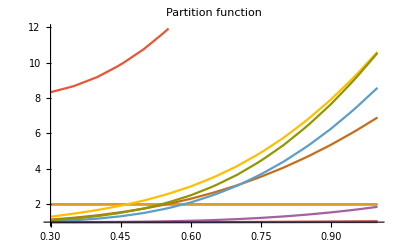

```mathematica
Plot[Evaluate[Table[G[[ii]],{ii,1,niso}]],{kT,tempMIN,tempMAX},PlotLabel->"Partition function"]
```

```mathematica
A=Table[tbl[[i,5]],{i,1,niso}]
```

{1,1,4,12,16,44,54,56,56,62,57}

```mathematica
Z=Table[tbl[[i,3]],{i,1,niso}]
```

{0,1,2,6,8,22,26,26,28,28,27}

```mathematica
Ne=Table[tbl[[i,4]],{i,1,niso}];
```

```mathematica
Q=Table[tbl[[i,1]]*tbl[[i,5]],{i,1,niso}] //Chop;
```

```mathematica
Export["data/A.dat",ToString[N[A]]<>"\n\n","Text"]
Export["data/Z.dat",ToString[N[Z]]<>"\n\n","Text"]
Export["data/N.dat",ToString[N[Ne]]<>"\n\n","Text"]
Export["data/Q.dat",ToString[N[Q]]<>"\n\n","Text"]
Export["data/G0.dat",ToString[N[G0]]<>"\n\n","Text"]
```

data/A.dat

data/Z.dat

data/N.dat

data/Q.dat

data/G0.dat

```mathematica
Export["data/GkT.dat",GkTstring<>"\n\n","Text"]
```

data/GkT.dat

```mathematica
qe=SetPrecision[1.6021892*10^(-19),myPrecision];
h=SetPrecision[6.626176 10^(-34),myPrecision];
k=SetPrecision[1.380662 10^(-23),myPrecision];
mp=SetPrecision[1.672  10^(-27),myPrecision];
```

```mathematica
T=kT 10^6 qe /k
```

1.1604499870352047187941951640223252011002445734839926390095863420747882972206812556863658766469×10^10 kT

```mathematica
Precision[T]
```

95.699

```mathematica
(* thermal de Broglie wavelength *)
```

```mathematica
λ=Sqrt[h^2/(2 Pi mp k T)]
```

1.6150947165848605696398405619854210875480289672409667454037866167531010455909107394516490255626×10^-14 √(1/kT)

```mathematica
(* abundance table *)
```

```mathematica
X = Table[(1/2)*G[[k]]*
     (1000ρ/(2*mp))^(A[[k]] - 1)*
     λ^(3*(A[[k]] - 1))*
     A[[k]]^(5/2)*Xn^Ne[[k]]*
     Xp^Z[[k]]*E^(Q[[k]]/kT), 
    {k, 1, niso}];
```

```mathematica
X[[1]]
```

1/2 Xn (2.+                        3
InterpolatingFunction[{{--, 1}}, <>]
                        10[kT])

```mathematica
(* sum of the abundances equals to 1 *)
```

```mathematica
eq1=Sum[X[[ii]],{ii,1,niso}]-1;
```

```mathematica
(* electron fraction *)
```

```mathematica
eq2=Sum[ Z[[ii]]/A[[ii]]* X[[ii]],{ii,1,niso}]-Ye;
```

```mathematica
eq11 = eq1 /. {Xn->10^n,Xp->10^p}  ;
eq22 = eq2 /. {Xn->10^n,Xp->10^p}  ;
```

```mathematica
(* ContourPlot[{eq11,eq22} /. kT->0.6,{n,-16,0},{p,-16,0},PlotPoints->15] *)
```

```mathematica
np=Table[{temp,lgdens,{,}},{temp,kTtbl},{lgdens,lgdenstbl}] ;
```

```mathematica
Dimensions[np]
```

{15,9,3}

```mathematica
J11=D[eq11,n]//Simplify;
```

```mathematica
J12=D[eq11,p]//Simplify;
```

```mathematica
J21=D[eq22,n]//Simplify;
```

```mathematica
J22=D[eq22,p]//Simplify;
```

```mathematica
(* TODO, ParallelTable - not easy in this form, some work required, np could be overwritten !  Each kernel must create own copy. Testing required !*)
```

```mathematica
Table[
For[kk=1, kk≤Dimensions[np][[2]],kk++,
For[ii=Dimensions[np][[1]];guessn=Log10[1-Ye];guessp=Log10[Ye],ii≥1,ii--,
temp = np[[ii,kk]][[1]];
dens = np[[ii,kk]][[2]];
sol=FindRoot[{eq11,eq22} /. {kT->temp,ρ->10^dens},{{n,guessn},{p,guessp}},WorkingPrecision->64, Jacobian->({{J11,J12},{J21,J22}}/. {kT->temp,ρ->10^dens}),MaxIterations->2000]; 
nse={Xn->10^n,Xp->10^p} /.sol;
guessn=n /.sol;
guessp=p /. sol;
np[[ii,kk,3]]={guessn,guessp};
abundances=X /. nse /. {kT->temp,ρ->10^dens};
If[Abs[Tr[abundances]-1]>10^-52,
Print["Ye=",Ye,"\tkT=",N[temp,3],"\t","lg ρ=",N[dens,3 ],"\t",Tr[abundances]-1,"\t",Select[Flatten[abundances],#>1&],"\t",Select[Flatten[abundances],#<0&]
](*If ends*)
]
];
 ];
   Export["data/np_P_GkT_"<>ToString[NumberForm[N[Ye],{4,4}]]<>".dat",Flatten[Table[{np[[ii,kk]][[1]],np[[ii,kk]][[2]],np[[ii,kk]][[3,1]],np[[ii,kk]][[3,2]]},{ii,1,Dimensions[np][[1]]},{kk,1,Dimensions[np][[2]]}],1],"Table"] 
,{Ye,Yetbl[[2;;-2]]}]
```

{data/np_P_GkT_0.0010.dat,data/np_P_GkT_0.0100.dat,data/np_P_GkT_0.0500.dat,data/np_P_GkT_0.1000.dat,data/np_P_GkT_0.1500.dat,data/np_P_GkT_0.2000.dat,data/np_P_GkT_0.2500.dat,data/np_P_GkT_0.3000.dat,data/np_P_GkT_0.3500.dat,data/np_P_GkT_0.3750.dat,data/np_P_GkT_0.4000.dat,data/np_P_GkT_0.4250.dat,data/np_P_GkT_0.4500.dat,data/np_P_GkT_0.4750.dat,data/np_P_GkT_0.5000.dat,data/np_P_GkT_0.5250.dat,data/np_P_GkT_0.5500.dat,data/np_P_GkT_0.6000.dat,data/np_P_GkT_0.6500.dat,data/np_P_GkT_0.7000.dat,data/np_P_GkT_0.7500.dat,data/np_P_GkT_0.8000.dat,data/np_P_GkT_0.8500.dat,data/np_P_GkT_0.9000.dat,data/np_P_GkT_0.9500.dat,data/np_P_GkT_0.9900.dat,data/np_P_GkT_0.9990.dat}

```mathematica
(* Case Ye=0 *)
np0=Table[{temp,lgdens,{0,-Infinity}},{temp,kTtbl},{lgdens,lgdenstbl}] ;
```

```mathematica
Export["data/np_P_GkT_"<>ToString[NumberForm[N[Yetbl[[1]]],{4,4}]]<>".dat",Flatten[Table[{np0[[ii,kk]][[1]],np0[[ii,kk]][[2]],np0[[ii,kk]][[3,1]],np0[[ii,kk]][[3,2]]},{ii,1,Dimensions[np0][[1]]},{kk,1,Dimensions[np0][[2]]}],1],"Table"]
```

data/np_P_GkT_0.0000.dat

```mathematica
(* Case Ye=1 *)
np1=Table[{temp,lgdens,{-Infinity,0}},{temp,kTtbl},{lgdens,lgdenstbl}] ;
```

```mathematica
(* Flatten[Table[{np[[ii,kk]][[1]],np[[ii,kk]][[2]],np[[ii,kk]][[3,1]],np[[ii,kk]][[3,2]]},{ii,1,Dimensions[np][[1]]},{kk,1,Dimensions[np][[2]]}],1]  ;*)
```

```mathematica
(*  Export["H:/misiek/tmp/np_800_fine096.dat",%,"Table"] *)
```

```mathematica
(* Export["E://temp/np_3181_fine.dat",%,"Table"] *)
```

```mathematica
Export["data/np_P_GkT_"<>ToString[NumberForm[N[Yetbl[[-1]]],{4,4}]]<>".dat",Flatten[Table[{np1[[ii,kk]][[1]],np1[[ii,kk]][[2]],np1[[ii,kk]][[3,1]],np1[[ii,kk]][[3,2]]},{ii,1,Dimensions[np1][[1]]},{kk,1,Dimensions[np1][[2]]}],1],"Table"]
```

data/np_P_GkT_1.0000.dat

```mathematica
npTMP=Table[Import["data/np_P_GkT_"<>ToString[NumberForm[N[Ye],{4,4}]]<>".dat","Lines"],{Ye,Yetbl}];
```

```mathematica
Dimensions[npTMP]
```

{29,135}

```mathematica
npTMP[[1,2]]
```

3/10	13/2	0	-Infinity

```mathematica
(* Imports rational and arbitrary precision numbers *)
```

```mathematica
np=Table[Table[npTMP[[jj]][[ii]] //StringSplit // ToExpression //N,{ii,1,Dimensions[npTMP[[1]]][[1]]}],{jj,1,YeNum}];
```

```mathematica
Dimensions[np]
```

{29,135,4}

```mathematica
np[[1]][[3]][[4]]  //FullForm
```

DirectedInfinity[-1]

```mathematica
kT /. {kT->np[[1]][[1,1]]}
```

0.3

```mathematica
X[[2]]/. {kT->np[[1]][[2]][[1]],ρ->10^np[[1]][[2]][[2]],Xn->10^np[[1]][[2]][[3]],Xp->10^np[[1]][[2]][[4]]}
```

0.

```mathematica
MinPrecision=$MachinePrecision
```

15.9546

```mathematica
Precision[10^np[[1]][[12,4]]]
```

∞

```mathematica
Table[Table[X /. {kT->np[[jj]][[ii]][[1]],ρ->10^np[[jj]][[ii]][[2]],Xn->10^np[[jj]][[ii]][[3]],Xp->10^np[[jj]][[ii]][[4]]}//Tr,{ii,1,Dimensions[np[[jj]]][[1]],10}] //Sort ,{jj,1,YeNum}]
(* Simple test; Expected result: only "1." *)
```

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
ToString[NumberForm[N[Yetbl[[1]]],{4,4}]]
```

0.0000

```mathematica
(* Export files for NSE_pn_table_parser.c; NOTE: NumberForm assume that 4 digits is enough for Ye tabulation *)
```

```mathematica
For[kk=1,kk≤YeNum,kk++,
Xntbl=Table[{N[np[[kk]][[jj,1]]],N[np[[kk]][[jj]][[2]]],N[10^np[[kk]][[jj]][[3]]]},{jj,1,Dimensions[np[[kk]]][[1]]}];
Xptbl=Table[{N[np[[kk]][[jj,1]]],N[np[[kk]][[jj]][[2]]],N[10^np[[kk]][[jj]][[4]]]},{jj,1,Dimensions[np[[kk]]][[1]]}];
name1="data/X_n_"<>ToString[NumberForm[N[Yetbl[[kk]]],{4,4}]]<>".dat";
name2="data/X_p_"<>ToString[NumberForm[N[Yetbl[[kk]]],{4,4}]]<>".dat";
Print[name1<>"\n"];
   Export[name1,Xntbl,"TSV"];
Export[name2,Xptbl,"TSV"]
]
(* 
DO NOT FORGET to run "./NSE_pn_table_parser >../data/np_table.c" from libnse directory before re-build !!!!!
*)
```

data/X_n_0.0000.dat

data/X_n_0.0010.dat

data/X_n_0.0100.dat

data/X_n_0.0500.dat

data/X_n_0.1000.dat

data/X_n_0.1500.dat

data/X_n_0.2000.dat

data/X_n_0.2500.dat

data/X_n_0.3000.dat

data/X_n_0.3500.dat

data/X_n_0.3750.dat

data/X_n_0.4000.dat

data/X_n_0.4250.dat

data/X_n_0.4500.dat

data/X_n_0.4750.dat

data/X_n_0.5000.dat

data/X_n_0.5250.dat

data/X_n_0.5500.dat

data/X_n_0.6000.dat

data/X_n_0.6500.dat

data/X_n_0.7000.dat

data/X_n_0.7500.dat

data/X_n_0.8000.dat

data/X_n_0.8500.dat

data/X_n_0.9000.dat

data/X_n_0.9500.dat

data/X_n_0.9900.dat

data/X_n_0.9990.dat

data/X_n_1.0000.dat

```mathematica
MaxMemoryUsed[]
```

194676864

```mathematica
(*
!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!

END of section required for libnse. Run

gcc NSE_pn_table_parser.c -o NSE_pn_table_parser 

NSE_pn_table_parser >np_table.c

 from your "data/" directory and recompile library (make; make install)

!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!
*)
```

```mathematica
(*

This section is required for NSE neutrinos

*)
```

```mathematica
Quit[]
```

```mathematica
fuller1=Import["E:/temp/fullerdat_nue.txt","Lines"];
fuller2=Import["E:/temp/fullerdat_nuebar.txt","Lines"];
```

```mathematica
(* Convert ffn isotope names to mathematica format (strings only! ) *)
```

```mathematica
namefix[s_]:=ToUpperCase[Characters[StringReplace[s," "->""]][[1]]] <>StringDrop[StringReplace[s," "->""],1]
```

```mathematica
ffniso1=Table[{ii,namefix[StringTake[fuller1[[ii*149+3]],{29,32}]]},{ii,0,188,1}] ;
ffniso2=Table[{ii,namefix[StringTake[fuller2[[ii*149+3]],{28,31}]]},{ii,0,188}] ;
```

```mathematica
(* positions of FFN isotopes in our NSE table, required for calculating neutrino spectra, not required for pure NSE calculations  *)
```

```mathematica
ffniso1[[3]]
```

```mathematica
FFNiso1=Table[IsotopeData[ffniso1[[ii,2]],"StandardName"],{ii,1,189}];
```

```mathematica
FFNiso2=Prepend[Table[IsotopeData[ffniso2[[ii,2]],"StandardName"],{ii,2,189}],"Neutron"]
```

```mathematica
A=Prepend[Table[IsotopeData[ffniso2[[ii]][[2]],"AtomicNumber"],{ii,2,189}],1]
```

```mathematica
Z=Prepend[Table[IsotopeData[ffniso2[[ii]][[2]],"MassNumber"],{ii,2,189}],0]
```

```mathematica
Nn=Prepend[Table[IsotopeData[ffniso2[[ii]][[2]],"NeutronNumber"],{ii,2,189}],1]
```

```mathematica
Table[If[Position[FFNiso2,IsotopeData[{iz,iz+in},"StandardName"]]=={},-1,Position[FFNiso2,IsotopeData[{iz,iz+in},"StandardName"]]]//First//First,{iz,0,39},{in,0,39}]
```

```mathematica
Position[18,%]
```

```mathematica
nueEnum=Table[Position[iso,IsotopeData[ffniso1[[ii,2]],"StandardName"]][[1,1]]-1,{ii,1,189}]
```

```mathematica
nuebarEnum=Insert[Table[Position[iso,IsotopeData[ffniso2[[ii,2]],"StandardName"]][[1,1]]-1,{ii,2,189}],0,1]
```

```mathematica
nuclideTBL=Table[If[Position[iso,IsotopeData[{ii,ii+jj},"StandardName"]]=={},-1,0],{ii,0,Zmax},{jj,0,Nmax}];
```

```mathematica
MatrixPlot[nuclideTBL]
```

```mathematica
FFNnue=Table[IsotopeData[(ffniso1 //Transpose //Last)[[ii]],"Symbol"],{ii,1,189}];
```

```mathematica
ffniso2[[1]]
```

```mathematica
FFNnuebar=Table[IsotopeData[(ffniso2 //Transpose //Last)[[ii]],"Symbol"],{ii,2,189}];
```

```mathematica
nueTBL=Table[If[Position[FFNnue,IsotopeData[{ii,ii+jj},"Symbol"]]=={},0,1],{ii,0,Zmax},{jj,0,Nmax}];
```

```mathematica
nuebarTBL=Table[If[Position[FFNnuebar,IsotopeData[{ii,ii+jj},"Symbol"]]=={},0,2],{ii,0,Zmax},{jj,0,Nmax}];
```

```mathematica
nueTBL+nuebarTBL+nuclideTBL //TableForm
```

```mathematica
magick={{2,1},{9,8},{17,16},{21,20},{29,28},{51,50},{Nmax+1,Nmax}}
```

```mathematica
MatrixPlot[nueTBL+nuebarTBL+nuclideTBL,ColorRules->{-1->White,0->Black,1->Blue,2->Green,3->Red}, DataReversed->{True,False},Mesh->True, FrameTicks->{ magick,magick,None ,None }]
```

```mathematica
IsotopeData["Properties"]
```

```mathematica
IsotopeData[iso[[34]],"Symbol"]
```

```mathematica
IsotopeData["Nickel56","FullSymbol"]
```